# Visualizations for the Quantum Bouncer

## Yen Lee Loh and Chee Kwan Gan, 2021-5-30

## Section General-purpose setup

### Section.Subsection Basics

```mathematica
Solid=Dashing@{};
DarkGreen=Darker[Green,0.67];
resistorColorList={Black,Brown,Red,Orange,Darker@Yellow,Darker@Green,Blue,Purple,Gray,Cyan};
resistorColor[n_Integer]:=resistorColorList⟦Mod[n+1,Length@resistorColorList,1]⟧;
resistorStyle[n_Integer]:={AbsoluteThickness@1,resistorColorList[[Mod[n,Length@resistorColorList,1]]]};
purpleWhite[v_]:=Hue[0.75,0.25,Abs[v]^0.5];
blueWhiteRed[v_]:=Hue[If[v>0.5,0.0,0.5],(2Abs[v-0.5]),0.95];
colorFromReal[x_,OptionsPattern[{Brightness->1.}]]:=Hue[If[x>0,0.,.5],0.8,1-1/(1+Abs[x*OptionValue[Brightness]])];
colorFromComplex[z_,OptionsPattern[{Brightness->1.}]]:=Hue[Rescale[Arg@z,{0,2 π}],0.8,1-1/(1+Abs[z*OptionValue[Brightness]])];
enlargeFont=#/.s_String->Style[s,16]&;
myCF=Blend[{
Hue[0.8,0.75,0.75],
Hue[0.7,0.75,0.80],
Hue[0.6,0.75,0.90],
Hue[0.6,0.25,1.00],
White,
RGBColor[0.9938925000000001,0.989345,0.5766145],
RGBColor[0.955963,0.863115,0.283425],
RGBColor[0.881316,0.5539655,0.2226795],
RGBColor[0.817319,0.134167,0.164218]},
Clip[#,{0,1}]]&;
myCF=Blend[{
Hue[0.67,0.75,0.80],
White,
Hue[.15,.75,.80]},
Clip[#,{0,1}]]&;
```

```mathematica
myGS={BaseStyle->{14,FontFamily->"Times",Black}};
myPS={LabelStyle->{14,FontFamily->"Times",Black},ImageSize->324,RotateLabel->False,Frame->True,FrameStyle->Directive@{AbsoluteThickness@0,Black},ImageMargins->1};
myPS1={PlotStyle->ColorData[97]};
SetOptions[Graphics,myGS];
SetOptions[Plot,myGS,myPS,ExclusionsStyle->Automatic];
SetOptions[ParametricPlot,myGS,myPS,ExclusionsStyle->Automatic];
SetOptions[ListPlot,myGS,myPS,myPS1];
SetOptions[ListLinePlot,myGS,myPS,myPS1];
SetOptions[ListLogPlot,myGS,myPS];
SetOptions[ListLogLogPlot,myGS,myPS];
SetOptions[ListLogLinearPlot,myGS,myPS];
SetOptions[ArrayPlot,myGS,myPS,AspectRatio->Automatic,PlotRangePadding->0];
SetOptions[ContourPlot,myGS,myPS,AspectRatio->Automatic,PlotRangePadding->0];
SetOptions[DensityPlot,myGS,myPS,AspectRatio->Automatic,PlotRangePadding->0];
SetOptions[StreamPlot,myGS,myPS,AspectRatio->Automatic,StreamColorFunction->None,StreamStyle->AbsoluteThickness@1];
SetOptions[Graphics3D,PlotRange->All,ImageSize->600,ViewPoint->{-1,-2,1},ViewVertical->{0,0,1},Lighting->"Neutral",Boxed->False,AspectRatio->Automatic];
```

### Section.Subsection Dimension lines (relatively new code: 2021-2-16)

```mathematica
(*---- USER MAY WANT TO TWEAK ARROWSIZE ----*)
dimLine[r1_,r2_,label_,tickLen_,arrowOffset_,labelOffset_]:=Module[{p,u,v,w,
arrowSize=0.015,
grAH=
Graphics[Line@{{-1,.3},{0,0},{-1,-.3}}]
(*Graphics[Polygon@{{-1,.5},{0,0},{-1,-.5}}]*)
},
p=r2-r1;u=Normalize@{-p⟦2⟧,p⟦1⟧};p=Normalize@p;
(*-------- CHECK IF DIMENSION IS SUFFICIENTLY LARGE --------*)
If[
Norm[r2-r1]>.8    (*5Max[tickLen,arrowOffset,labelOffset]*)
,
(*-------- ORDINARY INTERIOR DIMENSION LINE --------*)
{
Arrowheads[{{-arrowSize,Automatic,grAH},{arrowSize,Automatic,grAH}}],Arrow@{r1+arrowOffset*u,r2+arrowOffset*u},
Line@{{r1,r1+tickLen*u},{r2,r2+tickLen*u}},
Text[label,.55r1+.45r2+labelOffset*u]
},
(*-------- SPECIAL EXTERIOR DIMENSION LINE --------*)
{
exteriorLength=1;
Arrowheads[{{arrowSize,Automatic,grAH}}],
Arrow@{r2+exteriorLength*p+arrowOffset*u,r2+arrowOffset*u},
Arrow@{r1-exteriorLength*p+arrowOffset*u,r1+arrowOffset*u},
Line@{{r1,r1+tickLen*u},{r2,r2+tickLen*u}},
Text[label,.55r1+.45r2+labelOffset*u]
}
]
];
groundSymbol[{x_,y_},s_]:=(
Line@{{{0,3},{0,6}},{{-3,3},{3,3}},{{-2,2},{2,2}},{{-1,1},{1,1}}}
)//Translate[#,{0,-6}]&//Scale[#,s,{0,0}]&//Translate[#,{x,y}]&;
```

### Section.Subsection myFormat

```mathematica
(*-------- Pretty-print any real number --------*)
myFormat[v_]:=(
Which[
(*---- If v is an exact power of 10 with an exponent less than -4 or greater than +4, display v as 10^w ----*)
v>0&&Abs@Log10@v>5&&FractionalPart[Log10@v]==0,SuperscriptBox[10,Round@Log10@v],
(*---- If v is an integer, display v without any decimal points ----*)
Abs[v-Round@v]<10^-8,Round@v,
(*---- If v is not an integer, display v with decimals and possibly in scientific notation ----*)
True,NumberForm[N@v,ExponentFunction->(If[-4<#<4,Null,#]&),NumberPoint->"."]
](*//Style[#,FontWeight->Bold]&*));
```

### Section.Subsection Axis utilities: divisions, etc.

Let v be the numerical part of a physical quantity, and let x be the coordinate along the axis on which this quantity is plotted.
For example, suppose we are displaying 200 GHz at coordinate 8.3.  Then v=200×10^11 and x=8.3.
We will supply a conversion function vfromx to the myAxis function.

```mathematica
(*-------- Plotting parameters --------*)
maxMajorDivisions=30;
maxMinorDivisions=300;
tickLengthMajorP=0.25;
tickLengthMajorM=0.;
tickLengthMinorP=0.15;
tickLengthMinorM=0.;
textOffset=1.5;
(*-------- Round up or down to closest number in a list --------*)
roundUp[x_,xlist_]:=Min@Select[xlist,#≥x&];
roundDn[x_,xlist_]:=Max@Select[xlist,#≤x&];
(*-------- Round up or down to the nearest number of the form 1×10^n, 2×10^n, or 5×10^n --------*)
roundUpNicely[x_]:=Module[{expon},expon=Floor@Log10[x];roundUp[x/10^expon,{1,2,5,10}]*10^expon];
roundDnNicely[x_]:=Module[{expon},expon=Floor@Log10[x];roundDn[x/10^expon,{1,2,5,10}]*10^expon];
(*-------- Divide an interval to find a nice set of tick values --------*)
divisions[{vmin_,vmax_},maxDivisions_]:=Module[{vrange,vstep,vstart,lmin,lmax,v,divs},
vrange=vmax-vmin;
vstep=roundUpNicely[vrange/maxDivisions];
vstart=vstep*Ceiling[vmin/vstep];
divs=Select[Range[vstart,vmax,vstep],vmin≤#≤vmax&];
Return@divs;
];
(*-------- Divide an interval to find nice major and minor tick values --------*)
divisions[{vmin_,vmax_},{maxMajorDivisions_,maxMinorDivisions_}]:=Module[{vrange,vstep,vstart,lmin,lmax,v,majDivs,minDivs},
vrange=vmax-vmin;
vstep=roundUpNicely[vrange/maxMajorDivisions]; (* major division spacing *)
vstart=vstep*Ceiling[vmin/vstep];
majDivs=Select[Range[vstart,vmax,vstep],vmin≤#≤vmax&];
vstep=roundUpNicely[vstep/maxMinorDivisions]; (* minor division spacing *)
vstart=vstep*Ceiling[vmin/vstep];
minDivs=Select[Range[vstart,vmax,vstep],vmin≤#≤vmax&];
minDivs=Complement[minDivs,majDivs];
Return@{majDivs,minDivs}];
(*-------- Divide an interval with major ticks as 10^n and minor ticks as {2,3,4,5,6,7,8,9}×10^n --------*)
(*-------- This works well except when we have a very small interva --------*)
logDivisions[{vmin_,vmax_}]:=Module[{lmin,lmax,v,majDivs,minDivs}, (* l===Log10[v] *)
lmin=Floor@Log10@vmin;
lmax=Ceiling@Log10@vmax;
majDivs=Table[v=10^l;If[vmin≤v≤vmax,Sow@v],{l,lmin,lmax}]//Reap//Last//Last;
minDivs=Table[v=10^l*mantissa;If[vmin≤v≤vmax,Sow@v],{l,lmin,lmax},{mantissa,2,9}]//Reap//Last//Last;
Return@{majDivs,minDivs}];
linScale[label_,{xmin_,xmax_},vx_]:=Module[{vmin,vmax,xv,x},
xv=InverseFunction[vx];
{vmin,vmax}=Sort@(vx/@{xmin,xmax});
{vlist,vlist2}=divisions[{vmin,vmax},{30,6}];
vlist2=Flatten@vlist2;
Graphics[{
(*-------- Draw axis line and axis label --------*)
Text[label,{xmin,0},{2.00,0}],
{Line@{{xmin,0},{xmax,0}}},
(*-------- Draw major and minor tick marks --------*)
Table[x=xv[v];If[xmin≤x≤xmax,Line@{{x,-tickLengthMajorM},{x,tickLengthMajorP}}],{v,vlist}],
Table[x=xv[v];If[xmin≤x≤xmax,Line@{{x,-tickLengthMinorM},{x,tickLengthMinorP}}],{v,vlist2}],
(*-------- Draw major tick labels --------*)
Table[x=xv[v];If[xmin≤x≤xmax,Text[v//myFormat//DisplayForm,{x,0},{0,textOffset}]],{v,vlist}]
},
PlotRange->{{xmin,xmax},{-.5,.5}},PlotRangePadding->{{Scaled@.05,Scaled@.01},{0,0}},
ImageSize->{1200,50},AspectRatio->Full,BaseStyle->{18,FontFamily->"Times"}]
];
logScale[label_,{xmin_,xmax_},vx_]:=Module[{vmin,vmax,xv,x},
xv=Quiet@InverseFunction[vx];
{vmin,vmax}=Sort@(vx/@{xmin,xmax});
{vlist,vlist2}=myLogDivisions[{vmin,vmax}];vlist2=Flatten@vlist2;
(*-------- Draw axis line and axis label --------*)
Graphics[{
Text[label,{xmin,0},{2.00,0}],
Line@{{xmin,0},{xmax,0}},
(*-------- Draw major and minor tick marks --------*)
Table[x=xv[v];If[xmin≤x≤xmax,Line@{{x,-tickLengthMajorM},{x,tickLengthMajorP}}],{v,vlist}],
Table[x=xv[v];If[xmin≤x≤xmax,Line@{{x,-tickLengthMinorM},{x,tickLengthMinorP}}],{v,vlist2}],
(*-------- Draw major tick labels --------*)
Table[x=xv[v];If[xmin≤x≤xmax,Text[v//myFormat//DisplayForm,{x,0},{0,textOffset}]],{v,N@vlist}]
},
PlotRange->{{xmin,xmax},{-.5,.5}},PlotRangePadding->{{Scaled@.05,Scaled@.01},{0,0}},
ImageSize->{1200,50},AspectRatio->Full,BaseStyle->{18,FontFamily->"Times"}]
];
mark[x_,label_]:=Module[{},
{Line@{{x,-10},{x,-.5}},
Text[label,{x,-.5}]}
];
 stackScales[grList_]:=Module[{nmax=Length@grList},
Graphics[{
Table[
(*Inset[grList⟦n⟧,{0,-n}]*)
Translate[grList⟦n⟧⟦1⟧,{0,-n}]
,{n,nmax}],
},
ImageSize->{1200,50*nmax},AspectRatio->Full,
PlotRange->{All,{-nmax-.7,-.1}}
]
]
makeLabeledTicks[xmin_,xmax_]:=Module[{xMajorTicks,xMinorTicks,nMajorTicks=10,nMinorTicks=5,func=myFormat},
{xMajorTicks,xMinorTicks}=divisions[{xmin,xmax},{nMajorTicks,nMinorTicks}];
Join[
{N@#,func@#,{.02,0}}&/@xMajorTicks,
{N@#,Null,{.01,0}}&/@xMinorTicks
]
];
makeUnlabeledTicks[xmin_,xmax_]:=Module[{xMajorTicks,xMinorTicks,nMajorTicks=10,nMinorTicks=5,func=Null&},
{xMajorTicks,xMinorTicks}=divisions[{xmin,xmax},{nMajorTicks,nMinorTicks}];
Join[
{N@#,func@#,{.02,0}}&/@xMajorTicks,
{N@#,Null,{.01,0}}&/@xMinorTicks
]
];
```

### Section.Subsection autoTicksLabeled, etc.

```mathematica
decimalExponent[x_]:=Floor@Log10[x];
decimalMantissa[x_]:=x/(10^Floor@Log10[x]);
roundUpNicely[x_]:=SelectFirst[{1,2,5,10},#≥decimalMantissa[x]&]*10^decimalExponent[x];
divisions[{xmin_,xmax_},xstep_]:=Range[Ceiling[xmin,xstep],xmax,xstep]//Select[#,xmin≤#≤xmax&]&;
```

```mathematica
autoTicks$TickColor=White; (* MAY NEED TO SET THIS THING *)
autoTicksLabeled[xmin_,xmax_,nMajorTicks_:20,majorTickLen_:0.03,minorTickLen_:0.02]:=Module[{majorTicks,minorTicks},
majorTicks=divisions[{xmin,xmax},roundUpNicely[(xmax-xmin)/nMajorTicks]];
minorTicks=divisions[{xmin,xmax},roundUpNicely[(xmax-xmin)/nMajorTicks/5]]~Complement~majorTicks;
Join[{#,myFormat@N@#,{majorTickLen,0},autoTicks$TickColor}&/@majorTicks,{#,,{minorTickLen,0},autoTicks$TickColor}&/@minorTicks]
];
autoTicksUnlabeled[xmin_,xmax_,nMajorTicks_:20,majorTickLen_:0.03,minorTickLen_:0.02]:=Module[{majorTicks,minorTicks},
majorTicks=divisions[{xmin,xmax},roundUpNicely[(xmax-xmin)/nMajorTicks]];
minorTicks=divisions[{xmin,xmax},roundUpNicely[(xmax-xmin)/nMajorTicks/5]]~Complement~majorTicks;
Join[{#,,{majorTickLen,0},autoTicks$TickColor}&/@majorTicks,{#,,{minorTickLen,0},autoTicks$TickColor}&/@minorTicks]
];
autoContours=Function[{zmin,zmax},FindDivisions[{zmin,zmax},50]];
```

### Section.Subsection timeIt

```mathematica
SetAttributes[timeIt,HoldAll];
timeIt[cmds_]:=Module[{report,absTime,cpuTime},
report=AbsoluteTiming[Timing[cmds;]];
absTime=report⟦1⟧;
cpuTime=report⟦2,1⟧;
Print[StringForm["Absolute time = ``    CPU time = ``",absTime//DecimalForm[#,3]&,cpuTime//DecimalForm[#,3]&]]
];
```

### Section.Subsection myIntegerPlot, myRealPlot, myComplexPlot

```mathematica
colorFromInteger[n_]:=resistorColorList⟦Mod[n+1,10,1]⟧;
```

```mathematica
myIntegerPlot[xi_,yj_,zij_,opts:OptionsPattern[ArrayPlot]]:=Module[{},
gr=ArrayPlot[
Reverse@Transpose@zij,
opts,
DataRange->{{Min@xi,Max@xi},{Min@yj,Max@yj}},
PlotRange->{{Min@xi,Max@xi},{Min@yj,Max@yj}},PlotRangePadding->0,
ColorFunction->colorFromInteger,ColorFunctionScaling->False,
Frame->True,FrameTicks->{{autoTicksLabeled[#1,#2,10,.02,.01]&,autoTicksUnlabeled[#1,#2,10,.02,.01]&},{autoTicksLabeled,autoTicksUnlabeled}},
ImageSize->{648,216},AspectRatio->Full]
];
```

```mathematica
myRealPlot[xi_,yj_,zij_,opts:OptionsPattern[ArrayPlot]]:=Module[{},
gr=ArrayPlot[
Reverse@Transpose@zij,
opts,
DataRange->{{Min@xi,Max@xi},{Min@yj,Max@yj}},
PlotRange->{{Min@xi,Max@xi},{Min@yj,Max@yj}},PlotRangePadding->0,
ColorFunction->colorFromReal,ColorFunctionScaling->False,
Frame->True,FrameTicks->{{autoTicksLabeled[#1,#2,10,.02,.01]&,autoTicksUnlabeled[#1,#2,10,.02,.01]&},{autoTicksLabeled,autoTicksUnlabeled}},
ImageSize->{648,216},AspectRatio->Full]
];
```

```mathematica
myComplexPlot[xi_,yj_,zij_,opts:OptionsPattern[ArrayPlot]]:=Module[{},
gr=ArrayPlot[
Reverse@Transpose@zij,
opts,
DataRange->{{Min@xi,Max@xi},{Min@yj,Max@yj}},
PlotRange->{{Min@xi,Max@xi},{Min@yj,Max@yj}},PlotRangePadding->0,
ColorFunction->colorFromComplex,ColorFunctionScaling->False,
Frame->True,FrameTicks->{{autoTicksLabeled[#1,#2,10,.02,.01]&,autoTicksUnlabeled[#1,#2,10,.02,.01]&},{autoTicksLabeled,autoTicksUnlabeled}},
ImageSize->{648,216},AspectRatio->Full]
];
```

### Section.Subsection BeginPackage

```mathematica
BeginPackage["YLL`"];

Clear[YLLTicks];
Clear[YLLGraphicsGrid];

YLLGraphicsGrid::usage=
"YLLGraphicsGrid[grMat] displays the list of lists of Graphics objects, grMat, in a grid form.  See examples.";
Bleed::usage="Bleed is an option for YLLGraphicsGrid that specifies extra space to leave around each item.";
XTicksMain::usage="YLLGraphicsGrid[...,XTicksMain→func] applies the function func[xmin,xmax] to generate x-axis ticks on bottom-most panels.";
XTicksInternal::usage="YLLGraphicsGrid[...,XTicksInternal→func] applies the function func[xmin,xmax] to generate x-axis ticks on internal panels.";
ColumnSize::usage="See YLLGraphicsGrid.";
RowSize::usage="See YLLGraphicsGrid.";

Begin["Private`"];
```

### Section.Subsection YLLNumberForm

```mathematica
(*-------- Pretty-print any real number --------*)
YLLNumberForm[v_]:=Which[
(*---- If v is an exact power of 10 with an exponent less than -4 or greater than +4, display v as 10^w ----*)
v>0&&Abs@Log10@v>5&&FractionalPart[Log10@v]==0,SuperscriptBox[10,Round@Log10@v],
(*---- If v is an integer, display v without any decimal points ----*)
Abs[v-Round@v]<10^-8,Round@v,
(*---- If v is not an integer, display v with decimals and possibly in scientific notation ----*)
True,NumberForm[N@v,ExponentFunction->(If[-4<#<4,Null,#]&),NumberPoint->"."]
];
```

### Section.Subsection YLLTicks

```mathematica
decimalExponent[x_]:=Floor@Log10[x];
decimalMantissa[x_]:=x/(10^Floor@Log10[x]);
roundUpNicely[x_]:=SelectFirst[{1,2,5,10},#≥decimalMantissa[x]&]*10^decimalExponent[x];
divisions[{xmin_,xmax_},xstep_]:=Range[Ceiling[xmin,xstep],xmax,xstep]//Select[#,xmin≤#≤xmax&]&;
```

```mathematica
Options[YLLTicks]={TickFormat->Default,MajorTickCount->10,MajorTickLength->0.03,MinorTickLength->0.015,TickColor->Black};
YLLTicks[{xmin_,xmax_},opts1:OptionsPattern[]]:=Module[{
xMajor,xMinor,nMajor,lMajor,lMinor,color,fmtFunc
},
nMajor=OptionValue@MajorTickCount;
lMajor=OptionValue@MajorTickLength;If[!ListQ@lMajor,lMajor={lMajor,0}];
lMinor=OptionValue@MinorTickLength;If[!ListQ@lMinor,lMinor={lMinor,0}];
color=OptionValue@TickColor;
fmtFunc=OptionValue@TickFormat/.{None->(Null&),False->(Null&),True->YLLNumberForm,Default->YLLNumberForm};
xMajor=divisions[{xmin,xmax},roundUpNicely[(xmax-xmin)/nMajor]];
xMinor=divisions[{xmin,xmax},roundUpNicely[(xmax-xmin)/nMajor/5]]~Complement~xMajor;
Join[{#,fmtFunc@N@#,lMajor,color}&/@xMajor,{#,,lMinor,color}&/@xMinor]
];
```

The following example shows four different tick specifications, one for each edge of the frame:

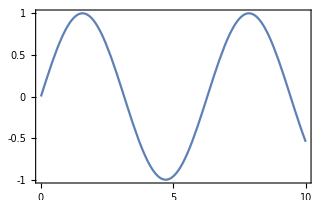

```mathematica
Plot[Sin[x],{x,0,10},
FrameTicks->{{
(* Left axis: use ranges supplied by Plot itself *)
YLLTicks[{#1,#2}]&,
(* Right axis: use same positions, but remove labels *)
Automatic                            
},{
(* Bottom axis: use a variety of options *)
YLLTicks[{0,10},TickFormat->YLLNumberForm,MajorTickCount->3,MajorTickLength->0.06,MinorTickLength->0.02,TickColor->Red],
(* Top axis: restrict range, suppress tick labels *)
YLLTicks[{3,6},TickFormat->None]
}}]
```

### Section.Subsection YLLGraphicsGrid

```mathematica
Options[YLLGraphicsGrid]={
ColumnSize->150,
RowSize->150,
Padding->{{64,10},{64,10}},
Bleed->32,
XTicksMain->(YLLTicks[{#1,#2},MajorTickCount->5]&),
YTicksMain->(YLLTicks[{#1,#2},MajorTickCount->5]&),
XTicksInternal->(YLLTicks[{#1,#2},MajorTickCount->5,TickFormat->None]&),
YTicksInternal->(YLLTicks[{#1,#2},MajorTickCount->5,TickFormat->None]&),
XLabel->"x",
YLabel->"y"
}~Join~Options@Graphics;
YLLGraphicsGrid[grMat_,opts1:OptionsPattern[]]:=Module[{
bleed,padding,gridLines,tickColor,grMat2,opts={opts1},
nCols,nRows,colSizes,rowSizes
},
(*-------- EXTRACT OPTIONS --------*)
colSizes=OptionValue@ColumnSize;
rowSizes=OptionValue@RowSize;
bleed=OptionValue[Bleed];
padding=OptionValue[Padding];
gridLines=OptionValue[GridLines];
xTicksMain=OptionValue[XTicksMain];(* For now this must be a single function. *)
yTicksMain=OptionValue[YTicksMain];(* Ultimately, we can allow multiple tick funcs. *)
xTicksInternal=OptionValue[XTicksInternal];
yTicksInternal=OptionValue[YTicksInternal];
(*-------- DETERMINE PARAMETERS --------*)
colMax=Dimensions[grMat]⟦2⟧;
rowMax=Dimensions[grMat]⟦1⟧;
If[ListQ@colSizes,colSizes=PadRight[colSizes,colMax,colSizes],colSizes=ConstantArray[colSizes,colMax]];
If[ListQ@rowSizes,rowSizes=PadRight[rowSizes,rowMax,rowSizes],rowSizes=ConstantArray[rowSizes,rowMax]];
colPositions=FoldList[Plus,0,{padding⟦1,1⟧,colSizes,padding⟦1,2⟧}//Flatten];
rowPositions=FoldList[Plus,0,{padding⟦2,1⟧,rowSizes,padding⟦2,2⟧}//Flatten];
(*-------- SET FRAME TICKS ON LEFT-MOST AND BOTTOM-MOST PANELS --------*)
grMat2=Table[
Show[grMat⟦m,n⟧,
Frame->{{True,n==colMax},{True,m==rowMax}},
FrameTicks->{{If[n==1,yTicksMain,yTicksInternal],None},{If[m==1,xTicksMain,xTicksInternal],None}},
FrameLabel->{If[m==1,OptionValue@XLabel,None],If[n==1,OptionValue@YLabel,None]}
]
,{m,rowMax}
,{n,colMax}
];
(*-------- CONSTRUCT GRAPHICS GRID --------*)
Graphics[
Table[
Show[
grMat2⟦row,col⟧,
PlotRangePadding->0,AspectRatio->Full,
ImageMargins->0,
ImagePadding->bleed*{{1,1},{1,1}}
]//Inset[#,{(colPositions⟦col+1⟧+colPositions⟦col+2⟧)/2,(rowPositions⟦row+1⟧+rowPositions⟦row+2⟧)/2},Center,{colSizes⟦col⟧+2*bleed,rowSizes⟦row⟧+2*bleed}]&
,{row,rowMax}
,{col,colMax}
],
GridLines->If[gridLines===Automatic,{colPositions,rowPositions},gridLines],
PlotRange->{{Min@colPositions,Max@colPositions},{Min@rowPositions,Max@rowPositions}},
ImageSize->{{Min@colPositions,Max@colPositions},{Min@rowPositions,Max@rowPositions}},
AspectRatio->Full,
Evaluate@FilterRules[opts, Options@Graphics](* pass on options to Graphics *)]
];
addTableHeadings2[matrixData_,rowHeadings_,colHeadings_]:=Module[{rows,cols,rowH,colH},rows=Dimensions[matrixData][[1]];
cols=Dimensions[matrixData][[2]];
rowH=PadRight[Graphics/@Text/@rowHeadings,rows,{}];
colH=PadRight[Graphics/@Text/@colHeadings,cols,{}];
ArrayFlatten[   {{{{  Graphics@{}  }},{colH}},{List/@rowH,matrixData}}   ]];
```

### Section.Subsection EndPackage

```mathematica
End[];
EndPackage[];
```

## Section One-Sided Bouncer (1SB)

### Section.Subsection Eigenvalues and eigenfunctions

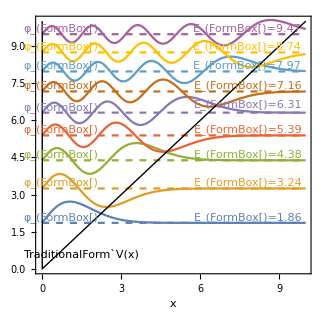

```mathematica
(*======== CLICK ANYWHERE IN THE CODE BELOW AND PRESS SHIFT+ENTER ========*)
nmax=9;     (* number of Airy functions to plot *)
xmax=10; (* plot range *)
ymax=10; (* plot range *)
ϵn[n_]:=-2.0^(-1/3)AiryAiZero[n];
φnx[n_,x_]:=2.0^(1/6)AiryAi[2.0^(1/3)x+AiryAiZero[n]]/AiryAiPrime[AiryAiZero[n]];
color[n_]:=ColorData[97][n];
gr=Show[
Plot[Table[ ϵn[n]+φnx[n,x],{n,1,nmax}]//Evaluate,{x,0,xmax}],
Plot[Table[ ϵn[n],{n,1,nmax}]//Evaluate,{x,0,xmax},PlotStyle->Dashed],
ImageSize->{324,324},AspectRatio->Full,
AxesOrigin->0,FrameLabel->{"x",""},
PlotRange->{{-0.05,xmax},{0,ymax}},PlotRangePadding->0,PlotRangeClipping->False,
Epilog->{Thick,Line@{{0,ymax},{0,0},{ymax/1.0,ymax}},
Table[{color[n],
Text[StringForm["E_(``)=``",n,ϵn[n]//N//NumberForm[#,3]&],{7.8,ϵn[n]+If[n==5,.1,0]},{0,-1.2}],
Text[StringForm["φ_(``)",n],{.7,ϵn[n]},{0,-1.2}]
},{n,nmax}],
Text["TraditionalForm`V(x)",{1.5,.6}]}
]
```

The figure above shows the potential V, stationary-state energies E_n, and eigenfunctions φ_n for the quantum bouncer in units where M=g=ℏ=1:
	V(x)=Piecewise[{{x, x>0}, {∞, x<0}}]
	E_n=-γ^-1 λ_n
	φ_n(x)=γ^(1/2)(Ai(γx+λ_n))/(Ai'(λ_n))
where λ_n is the nth zero of the Airy function and γ=2^(1/3).

### Section.Subsection Classical paths (interactive)

```mathematica
(*======== CLICK ANYWHERE IN THE CODE BELOW AND PRESS SHIFT+ENTER ========*)
DynamicModule[{tixi={0,10},tfxf={5,9},g=1,xi,xf,T,a,b,nmax,n,u,v,w,vi,uSols,viList,αα,xt,αmax,colorαList},
LocatorPane[
(*-------- Constrain locators differently --------*)
Dynamic[{tixi,tfxf},Switch[CurrentValue["CurrentLocatorPaneThumb"],1,tixi⟦2⟧=#⟦1,2⟧,2,tfxf=#⟦2⟧]&],
(*-------- Draw graphics --------*)
Row@{
Dynamic[
xi=tixi⟦2⟧;xf=tfxf⟦2⟧;T=tfxf⟦1⟧;g=1;
(*-------- CALCULATE NUMBER OF TRAJECTORIES --------*)
a=(2xi)/(g T^2);b=(2xf)/(g T^2);nmax=Ceiling[√(1+1/(2a+2b))];(*-------- n,u,v,w,vi,S,dSdxidxf ARE LISTS --------*)
{n,u}=Do[
uSols=Which[
n==0,{(1+b-a)/2},
n==1,Root[1-10 a+9 a^2+2 b+6 a b+b^2+(-4+20 a-4 b) #1+(-4+8 a+8 b) #1^2+16 #1^3&,#]&/@Range@3,
True,Root[16(n^4-n^2)#^4+16 n^2#^3+(32 n^4 a+8 n^2(b-1-3a)+4)#^2+4(4 n^2 a+a-b-1)#+(16 n^4 a^2+8 n^2 a(b-1-a)+(1+b-a)^2)&,#]&/@Range@4
]//N//Union//Select[#,Im[#]==0&]&;
Sow/@{{n,#}}&/@uSols;
,{n,0,nmax}]//Reap//Last//Last//Transpose;
vi=u g T;
w=√(u^2+a);
v=u-1+2n w;
αmax=Length@n;
αα=Range@αmax;
(*-------- CALCULATE TRAJECTORIES --------*)
xt[t_,vi_]:=Module[{vmax,k,tn},vmax=√(vi^2+2g xi);k=Floor[(g t-vi+vmax)/(2vmax)];tn=(vi-vmax)/g+k*(2vmax)/g;vmax(t-tn)-g/2 (t-tn)^2];
αmax=Length@αα;
colorαList=Hue[#,1,.7]&/@(Range[αmax]/αmax)//N;
(*-------- PLOT --------*)
Plot[
Table[xt[t,vi⟦α⟧],{α,αα}]//Evaluate,{t,0,T},
Frame->True,FrameLabel->{"Time t","Position\nx"},RotateLabel->True,
PlotStyle->Table[Directive@{AbsoluteThickness@0,resistorColor[n⟦α⟧]},{α,αmax}],
Epilog->{AbsolutePointSize@8,Black,Point@{0,xi},Point@{T,xf},
Text[StringForm["x_i=``",xi],Offset[{10,0},{0,xi}],{-1.,0}],
Text[StringForm["x_f=``",xf],{T,xf},{-1.5,0}]
},ImageSize->{648,324},AspectRatio->Full,PlotRange->{{0,20},{0,40}},PlotRangePadding->{{0,0},{0,0}},AxesOrigin->{0,0},ImagePadding->{{All,8},{All,8}},PlotRangeClipping->False,GridLines->{Range[20],Range[0,40,2]}
]
],
LineLegend[Table[Directive@{AbsoluteThickness@0,resistorColor[n]},{n,0,4}],Table[StringForm["n=``",n],{n,0,4}],LabelStyle->{FontFamily->"Times"}]
}
]]
```

In the demo above, drag the two locators to change the start and end points.

### Section.Subsection Feynman path integral in semiclassical approximation: infographic

#### Define code: analyze, findBounces, findFoci, findMorseIndexM, findXf, plotPathVi, plotPathWithWiggles (run this section)

```mathematica
analyze[xi_,xf_,T_,g_]:=Module[{a,b,uSols,nmax,n,viα,u,v,w,SαOverM,DαOverM,mα},
a=(2 xi)/(g T^2);b=(2 xf)/(g T^2);nmax=Ceiling[√(1+1/(2 a+2 b))];
{n,u}=Do[
uSols=Which[
n==0,{(1+b-a)/2},
n==1,Root[1-10 a+9 a^2+2 b+6 a b+b^2+(-4+20 a-4 b) #1+(-4+8 a+8 b) #1^2+16 #1^3&,#]&/@Range@3,
True,Root[16(n^4-n^2)#^4+16 n^2#^3+(32 n^4 a+8 n^2(b-1-3a)+4)#^2+4(4 n^2 a+a-b-1)#+(16 n^4 a^2+8 n^2 a(b-1-a)+(1+b-a)^2)&,#]&/@Range@4
]//N//Union//Select[#,Im[#]==0&]&;
Sow/@{{n,#}}&/@uSols;
,{n,0,nmax}]//Reap//Last//Last//Transpose;
viα=u g T;
w=√(u^2+a);v=u-1+2n w;
SαOverM=(g^2 T^3)/6(2(u^3-v^3)-3 w^2(u-v)-2n w^3);
DαOverM=1/T w^2/(u v+a v-b u);
mα=findMorseIndexM[T,#]&/@viα;
{viα,SαOverM,DαOverM,mα}
];
findBounces[xi_,vi_,T_,g_]:=Module[{tb,t0,vm,n},
vm=√(vi^2+2g xi);t0=vi/g;tb=(2vm)/g;n=Floor[(T-t0)/tb+1/2];t0+(Range[n]-1/2)tb
];
findFoci[xi_,vi_,T_,g_]:=Module[{vm,n,k0Floor,tF,xF,t0,tb,tFxFk},
vm=√(vi^2+2g xi);k0Floor=Floor[1/2(1-vm/vi)];n=⌈(g T-vi)/(2vm)⌉;t0=vi/g;tb=(2vm)/g;
tFxFk={};
Do[        
If[k==k0Floor,Continue[]];
tF=(2k)/g(vi^2+2k vi vm+vm^2)/(2k vi+vm);
xF=(vm^2/(2g)-g/2(tF-t0-tb Floor[(tF-t0)/tb+1/2])^2);
If[tF>T,Continue[]];
AppendTo[tFxFk,{tF,xF}];
,{k,n}];
Return[tFxFk];
];
findMorseIndexM[T_,vi_]:=Module[{vm,n,j,k,m},
vm=√(vi^2+2 g xi);
n=Floor[(g T-vi)/(2vm)+1/2];(* number of bounces *)
j=Floor[(g T-vi)/(2vm)]+UnitStep[vi];(* index n of strip [region between bounces] in which (T,vi) is located *)
k=j+UnitStep[-√(g xi)-vi √(2j(j+1))];
m=j+UnitStep[T-(2k)/g(vi^2+2k vi vm+vm^2)/(2k vi+vm)]+2n; (* note the n *)
Return[m]];
findXf[xi_,vi_,t_,g_]:=Module[{tb,t0,vm},
vm=√(vi^2+2g xi);t0=vi/g;tb=(2vm)/g;
vm^2/(2g)-g/2(t-t0-tb Floor[(t-t0)/tb+1/2])^2
];
plotPathVi[xi_,vi_,T_,g_,style_:Directive[AbsoluteThickness@0,Opacity[0.25,Black]] ]:=Module[{vm,xt,tb,t0,αmax,colorα},
vm=√(vi^2+2g xi);t0=vi/g;tb=(2vm)/g;     (* vm and tb are lists *)
xt=Function[{t},vm^2/(2g)-g/2(t-t0-tb Floor[(t-t0)/tb+1/2])^2];
Plot[Evaluate[xt[t]],{t,0,T},PlotStyle->style,Exclusions->None]];
plotPathWithWiggles[xi_,vi_,T_,g_,amp_:0.1,color_:Gray ]:=Module[{vm,xt,St,θt,M=1,ℏ=1,t,tb,t0,αmax,colorα},
vm=√(vi^2+2g xi);t0=vi/g;tb=(2vm)/g;     (* vm and tb are lists *)
xt[t_]=vm^2/(2g)-g/2(t-t0-tb Floor[(t-t0)/tb+1/2])^2;
St[t_]:=Module[{n,vf},n=Floor[(t-t0)/tb+1/2];vf=vi-g t+2n vm;M/(6g)(2(vi^3-vf^3)-3 vm^2(vi-vf)-2n vm^3)];
θt[t_]:=St[t]/ℏ+findMorseIndexM[t,vi];
Plot[{xt[t],xt[t]+amp*Cos[θt[t]](*,xt[t]+amp*Sin[θt[t]]*)},{t,0,T},
PlotStyle->{
{AbsoluteThickness@1,color},
{AbsoluteThickness@2,Lighter[color,.5]},
{AbsoluteThickness@2,CapForm@"Butt",AbsoluteDashing@{1,1},Lighter[color,.5]}},
Exclusions->None]];
```

#### Make infographic

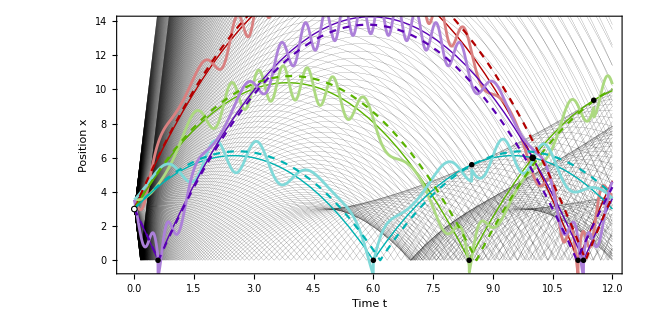
-Graphics-α | v_i^(α) | S_α | D_α | m_α
1 | 5.3 | -86.2 | -0.100 | 1
2 | 3.8 | -30.5 | 0.243 | 3
3 | 2.5 | -27.4 | -0.269 | 4
4 | -4.7 | -54.3 | 0.127 | 3

```mathematica
(*======== CLICK ANYWHERE IN THE CODE BELOW AND PRESS SHIFT+ENTER ========*)
(*-------- SET USER-DEFINED PARAMETERS --------*)
xi=3;   (* initial position *)
xf=6;   (* final position *)
T=10;   (* final time *)
g=1;     (* gravitational field strength *)
viList=Range[-20,20,.1];  (* list of initial velocities for plotting *)
dvi=0.1; (* perturbation of initial velocity *)
Tmax=T+2; (* maximum time for plotting *)
xmax=Max[xi,xf]*2+2; (* maximum position for plotting *)
wiggleAmp=1;   (* size of wiggles representing phase of particle *)
(*-------- FIND ALLOWED INITIAL VELOCITIES --------*)
{viα,SαOverM,DαOverM,mα}=Transpose@Reverse@Sort@Transpose@analyze[xi,xf,T,g];
αmax=Length@viα;colorα=Hue[#,1,.7]&/@(Range[0,αmax-1]/αmax)//N;
(*-------- UTILITIES --------*)
gpStar=Line@{{{-1,0},{1,0}},{{0,-1},{0,1}},{{-.71,-.71},{.71,.71}},{{-.71,.71},{.71,-.71}}};
gpDiamond=Line@{{1,0},{0,1},{-1,0},{0,-1},{1,0}};
myFrame@gr_:=gr//Framed[#,Background->White]&;
myFrameTranslucent@gr_:=gr//Framed[#,Background->Opacity[.7,White]]&;
myLegend=Table[{
α//Style[#,colorα⟦α⟧]&,
viα⟦α⟧//NumberForm[#,{∞,1}]&//Style[#,colorα⟦α⟧]&,
SαOverM⟦α⟧//NumberForm[#,{∞,1}]&//Style[#,colorα⟦α⟧]&,
DαOverM⟦α⟧//NumberForm[#,{∞,3}]&//Style[#,colorα⟦α⟧]&,
mα⟦α⟧//Style[#,colorα⟦α⟧]&
},{α,αmax}]//
TableForm[#,TableHeadings->{None,{"α","v_i^(α)","S_α","D_α","m_α"}}]&;
gr=Show[
(*-------- BACKGROUND PATHS --------*)
Table[    plotPathVi[xi,vi,Tmax,g,Directive[AbsoluteThickness@0.1,Black]]    ,{vi,viList}],
(*-------- CLASSICAL PATHS --------*)
(*Table[    plotPathVi[xi,viα⟦α⟧,Tmax,g,colorα⟦α⟧]    ,{α,αmax}],*)
Table[    plotPathWithWiggles[xi,viα⟦α⟧,Tmax,g,wiggleAmp,colorα⟦α⟧]    ,{α,αmax}],
(*-------- PERTURBED PATHS --------*)
Table[    plotPathVi[xi,viα⟦α⟧+dvi,Tmax,g,{Dashed,colorα⟦α⟧}]    ,{α,αmax}],
(*Table[    plotPathVi[xi,viα⟦α⟧-dvi,Tmax,g,{Dashed,colorα⟦α⟧}]    ,{α,αmax}],*)
(*-------- OTHER GRAPHICS --------*)
Graphics[{
(*-------- START AND END POINTS --------*)
Inset[Graphics[{FaceForm[White],EdgeForm@{Thick,Black},Disk[]}],{0,xi},{0,0},Scaled@.05],
Inset[Graphics[{FaceForm[Black],EdgeForm[Black],Disk[]}],{T,xf},{0,0},Scaled@.05],
(*-------- BOUNCES --------*)
Table[
tFxFk=findBounces[xi,viα⟦α⟧,Tmax,g];  (* let's plot all the way*)
Inset[Graphics[{colorα⟦α⟧,AbsoluteThickness@2,gpDiamond}],{#,0},{0,0},Scaled@.05]&/@tFxFk
  ,{α,αmax}],
(*-------- FOCI --------*)
Table[
tFxFk=findFoci[xi,viα⟦α⟧,Tmax,g];  (* let's plot all the way*)
Inset[Graphics[{colorα⟦α⟧,AbsoluteThickness@2,gpStar}],#,{0,0},Scaled@.05]&/@tFxFk
  ,{α,αmax}]
}
],
Frame->True,FrameLabel->{"Time t","Position x"},RotateLabel->True,
PlotRange->{{-.2,Tmax},{-.5,xmax}},PlotRangePadding->0,(*PlotRangeClipping->False,*)
ImageSize->{648,324},AspectRatio->Full,
AxesOrigin->{0,0},Axes->True,
ImagePadding->{{Automatic,Automatic},{Automatic,4}}];
Row@{gr,myLegend}
```

In most introductory courses on optics or modern physics, Young’s double-slit experiment is explained in terms of a semiclassical path integral.  A photon (or electron) passes simultaneously through two slits.  It travels along two paths, accumulating a different phase along each path as it propagates through air (or through optical elements or electric fields inserted along the path).  At each point on the screen, constructive or destructive interference occurs depending on the phase difference.  The visibility of the interference fringes depends upon the relative amplitudes of the rays from the slits.

The figure above explains the quantum bouncer in terms of these very same concepts.  Suppose a quantum particle (bouncing ball) is released at position x_i at time t=0, and is subsequently detected at position x_f at time T.  There may be more than one classical path from x_i to x_f.  As the particle travels along path X_α(t), it picks up a phase 
	θ_α(t)=1/ℏ S_α(t)-π/2 m_α(t)
where S_α(T)=∫_0^T dt  L(X_α(t),(Ẋ)_α(t)) is the classical action and m_α(t) is the Morse index.  Solid curves show classical paths X_α(t).  Dashed curves show paths resulting from slight perturbations of the initial velocity v_i.  The dashed curves and solid curves drift apart initially, but they converge again at foci (stars).  The Morse index m_α(T) is the number of foci along the path in the time interval 0≤t≤T.  The initial point (empty circle) counts as one focus.  A bounce (empty diamond) counts as two foci.  The phase factor θ_α(t) along each path is visualized as a wiggly curve, which has discontinuities at bounces and foci.  The amplitude of each path is √(1/(2πℏ)|D_α(t)|) where D_α(t) is the van Vleck determinant.  It may be shown that D_α(t)=-1/f_α(t) where the path divergence function, f_α(t)=∂X_α(t)/∂v_i, is the deviation between the solid curve and the dashed curve.  If path α has a focus near time T, then f_α(t) is small and D_α(t) is large.

The gray curves show many paths starting at x_i with different initial velocities v_i.  These paths overlap strongly along caustic curves.

### Section.Subsection Wavepacket evolution (animation)

#### Code

```mathematica
findEigs[xList_,nmax_:10000]:=Module[{M,g,ℏ,xUnit,EUnit,tUnit,λn,En,φnx},
M=g=ℏ=1;xUnit=(ℏ^2/(2g M^2))^(1/3);EUnit=((ℏ^2 g^2 M)/2)^(1/3);tUnit=((2ℏ)/(g^2 M))^(1/3);
λn=AiryAiZero[Range[1,nmax]]//N;
En=-λn EUnit;    (* find eigenvalues *)
φnx=xUnit^(-1/2)1/AiryAiPrime[λn]*Outer[AiryAi[#1+#2]&,λn,xList/xUnit];  (* find eigenvectors *)
Return@{En,φnx}
];
```

```mathematica
makeDeltaFunction[xList_,xPos_]:=Module[{xStep=xList⟦2⟧-xList⟦1⟧},Return@Table[If[Abs[x-xPos]≤xStep/2,1./xStep,0.],{x,xList}]];
makeWavePacket[xList_,{xCen_,xWid_,kCen_}]:=Return@Table[1/(√(√π xWid))Exp[-0.5((x-xCen)/xWid)^2]Exp[+I*kCen*(x-xCen)],{x,xList}];
findTimeEvolutionMatrix[En_,TList_]:=Return@Outer[Exp[-I #1 #2]&,En,TList];(* E and T should be dimensionless*)
```

#### Heatmaps

Precalculate eigenenergies E_n, eigenvectors φ_n(x), and time evolution factors exp(-i/ℏ E_n t_k):

```mathematica
xi=10;
xfList=Range[0,15,0.0625]; (* spatial grid *)
TList=Range[0.03125,25,0.03125]; (* time grid *)

{En,φnx}=findEigs[xfList,10000];(* prepare 10000 eigenvalues and eigenvectors *)
UnT=findTimeEvolutionMatrix[En,TList]; (* prepare time evolution matrix *)
```

Let Ψ(x,0)≈δ(x-x_i), appropriately discretized.  Calculate the expansion coefficients c_n(0)=∫_0^∞ dx φ_n(x)* Ψ(x,0)=δx∑_(n=1)^∞ U_nj Ψ(x,0).  Apply the time evolution matrix to obtain 	c_n(t)=∑_(n=1)^∞ [exp(-i/ℏ E_n t_k]c_n(0).  Transform back to real space to obtain Ψ(x,t)=∑_(n=1)^∞ φ_n(x) c_n(t).  Thus, visualize time evolution of a Dirac delta function, i.e., plot propagator K(x_f,T):

```mathematica
Ψx0=makeDeltaFunction[xfList,10.]; (* make initial wave packet *)
cn0=φnx.Ψx0*(xfList⟦2⟧-xfList⟦1⟧);(* transform to eigenbasis  *)
cnT=cn0*UnT;    (* apply time evolution matrix *)
ΨxT=cnTᵀ.φnx;    (* transform back to real space *)
gr=myComplexPlot[TList,xfList,2*ΨxT,FrameLabel->Reverse@{"t","x"},Epilog->{White,Text["Ψ(x,t)",Scaled@{0.1,1},{0,2}]}]
```

Visualize time evolution of a Gaussian wave packet with center position x_cen=10, width x_wid=1, and initial momentum k_cen=0:

```mathematica
Ψx0=makeWavePacket[xfList,{10,1,0}]; (* make initial wave packet *)
cn0=φnx.Ψx0*(xfList⟦2⟧-xfList⟦1⟧);(* transform to eigenbasis  *)
cnT=cn0*UnT;    (* apply time evolution matrix *)
ΨxT=cnTᵀ.φnx;    (* transform back to real space *)
gr=myComplexPlot[TList,xfList,2*ΨxT,FrameLabel->Reverse@{"t","x"},Epilog->{White,Text["Ψ(x,t)",Scaled@{0.1,1},{0,2}]}]
```

#### Animation

```mathematica
Ψx0=makeWavePacket[xfList,{10,1,0}]; (* make initial wave packet *)
cn0=φnx.Ψx0*(xfList⟦2⟧-xfList⟦1⟧);(* transform to eigenbasis  *)
```

```mathematica
{xmin,xmax}={Min@xfList,Max@xfList};
Manipulate[
(* May need to multiply by convergence factor Exp[.005*ζn] to suppress spurious ghosts at short times *)
cnT=cn0*Exp[-I*En*t];
ΨxT=cnT.φnx;
ListLinePlot[{Abs@ΨxT,Re@ΨxT,Im@ΨxT},PlotRange->{-1,1},PlotRangePadding->0,ImageSize->{648,324},AspectRatio->Full,
PlotStyle->{{Thick,Brown},{AbsoluteThickness@0,RGBColor[.3,.3,.7]},{AbsoluteThickness@0,Dashed,RGBColor[.3,.3,.7]}},
DataRange->{xmin,xmax}]
,{t,0.01,100,0.01,Appearance->"Open",AnimationRate->5}]
```

The animation above shows Ψ(x,t) versus x.  The curves are |Ψ|, Re Ψ, and Im Ψ.

### Section.Subsection Propagator visualized as heatmap

#### Code: KEE, KPI, KPIAmplitudeOnly

```mathematica
KEE[xfList_,xi_,TList_,M_,g_,ℏ_]:=Module[{nmax,xUnit,EUnit,tUnit},
nmax=10000;
λn=AiryAiZero[Range[1,nmax]]//N;
xUnit=(ℏ^2/(2g M^2))^(1/3);EUnit=((ℏ^2 g^2 M)/2)^(1/3);tUnit=((2ℏ)/(g^2 M))^(1/3);
En=-λn EUnit;    (* eigenvalues *)
φnxFunc[n_,x_]:=xUnit^(-1/2)AiryAi[λn⟦n⟧+x/xUnit]/AiryAiPrime[λn⟦n⟧];    (* eigenfunctions *)
φnj=xUnit^(-1/2)1/AiryAiPrime[λn]*Outer[AiryAi[#1+#2]&,λn,xfList/xUnit];    (* discrete eigenfunctions *)
Unk=Outer[Exp[-I #1 #2]&,En/EUnit,TList/tUnit];    (* time evolution matrix *)
cn0=Table[φnxFunc[n,xi],{n,1,nmax}];    (* initial coefficients *)
cnk=cn0*Unk;    (* evolved coefficients *)
KEEData=cnkᵀ.φnj;    (* propagator *)
Return@KEEData
];
```

```mathematica
KPI[xf_,xi_,T_,M_,g_,ℏ_]:=Module[{a,b,nmax,uSols,n,nα,u,v,w,S,dSdxidxf,j,k,m},
a=(2xi)/(g T^2);b=(2xf)/(g T^2);nmax=Ceiling[√(1+1/(2a+2b))];(*-------- n,u,v,w,vi,S,dSdxidxf ARE LISTS --------*)
{nα,u}=Do[
uSols=Which[
n==0,{(1+b-a)/2},
n==1,Root[1-10 a+9 a^2+2 b+6 a b+b^2+(-4+20 a-4 b) #1+(-4+8 a+8 b) #1^2+16 #1^3&,#]&/@Range@3,
True,Root[16(n^4-n^2)#^4+16 n^2#^3+(32 n^4 a+8 n^2(b-1-3a)+4)#^2+4(4 n^2 a+a-b-1)#+(16 n^4 a^2+8 n^2 a(b-1-a)+(1+b-a)^2)&,#]&/@Range@4
]//N//Union//Select[#,Im[#]==0&]&;
Sow/@{{n,#}}&/@uSols;
,{n,0,nmax}]//Reap//Last//Last//Transpose;
w=√(u^2+a);
v=u-1+2nα w;
S=(M g^2 T^3)/6(2(u^3-v^3)-3 w^2(u-v)-2nα w^3);
dSdxidxf=M/T w^2/(u v+a v-b u);
j=Floor[(1-u)/(2w)]+UnitStep[u];(* index n of strip [region between bounces] in which (T,vi) is located *)
k=j+UnitStep[-√a-2u √(j(j+1))];(* this is a different k from before *)
m=j+UnitStep[1-2k(u^2+2k u w+w^2)/(2k u+w)]+2nα;(* note the additional 2*number of bounces! *)
Total[√(I/(2π ℏ))√Abs[dSdxidxf]*Exp[(I*S)/ℏ-(I π)/2 m]]
];
```

```mathematica
KPIAmplitudeOnly[xf_,xi_,T_,M_,g_,ℏ_]:=Module[{a,b,nmax,uSols,n,nα,u,v,w,S,dSdxidxf,j,k,m},
a=(2xi)/(g T^2);b=(2xf)/(g T^2);nmax=Ceiling[√(1+1/(2a+2b))];(*-------- n,u,v,w,vi,S,dSdxidxf ARE LISTS --------*)
{nα,u}=Do[
uSols=Which[
n==0,{(1+b-a)/2},
n==1,Root[1-10 a+9 a^2+2 b+6 a b+b^2+(-4+20 a-4 b) #1+(-4+8 a+8 b) #1^2+16 #1^3&,#]&/@Range@3,
True,Root[16(n^4-n^2)#^4+16 n^2#^3+(32 n^4 a+8 n^2(b-1-3a)+4)#^2+4(4 n^2 a+a-b-1)#+(16 n^4 a^2+8 n^2 a(b-1-a)+(1+b-a)^2)&,#]&/@Range@4
]//N//Union//Select[#,Im[#]==0&]&;
Sow/@{{n,#}}&/@uSols;
,{n,0,nmax}]//Reap//Last//Last//Transpose;
w=√(u^2+a);
v=u-1+2nα w;
dSdxidxf=M/T w^2/(u v+a v-b u);
Total[√(1/(2π ℏ))√Abs[dSdxidxf]]
];
```

#### Calculate propagator for fixed x_i for various x_f and T

```mathematica
xi=10;
xfList=Range[0,15,0.03125]; (* fine position grid *)
TList=Range[0.03125,25,0.03125]; (* fine time grid *)
(*xi=10;
xfList=Range[0,15,8*0.0625]; (* coarse grid *)
TList=Range[0.03125,25,8*0.03125];*)
```

```mathematica
timeIt[  dataKEE=KEE[xfList,xi,TList,1,1,1]        ];
```

Absolute time = 49.7    CPU time = 50.1

```mathematica
Monitor[timeIt[  dataVVD=Table[KPIAmplitudeOnly[xf,xi,T,1,1,1],{T,TList},{xf,xfList}]        ],{T,xf}];
```

Absolute time = 658.    CPU time = 649.

```mathematica
Monitor[timeIt[  dataKPI=Table[KPI[xf,xi,T,1,1,1],{T,TList},{xf,xfList}]        ],{T,xf}];
```

Absolute time = 737.    CPU time = 665.

```mathematica
(*DumpSave[NotebookDirectory[]<>"/bouncer1.mx",{xi,TList,xfList,dataKEE,dataVVD,dataKPI}];*)
```

#### Load data and make graphics

```mathematica
Get[NotebookDirectory[]<>"/bouncer1.mx"];
```

```mathematica
scalFac=1;
grVVD=myComplexPlot[TList,xfList,scalFac*dataVVD,FrameLabel->Reverse@{"T","x_f"},Epilog->{White,Text["K_VVD",Scaled@{0.1,1},{0,1.5}]}];scalFac=2;
grPI=myComplexPlot[TList,xfList,scalFac*dataKPI,FrameLabel->Reverse@{"T","x_f"},Epilog->{White,Text["K_SCA",Scaled@{0.1,1},{0,1.5}]}];
grEE=myComplexPlot[TList,xfList,scalFac*dataKEE,FrameLabel->Reverse@{"T","x_f"},Epilog->{White,Text["K_EE",Scaled@{0.1,1},{0,1.5}]}];
grPIMinusEE=myComplexPlot[TList,xfList,scalFac*(dataKPI- dataKEE),FrameLabel->Reverse@{"T","x_f"},Epilog->{White,Text["K_SCA-K_EE",Scaled@{0.1,1},{0,1.5}]}];
```

```mathematica
gr=YLLGraphicsGrid[
{Reverse@{grVVD,grPI,grEE,grPIMinusEE}}ᵀ,
ColumnSize->600,(* column size(s) *)
RowSize->108,       (* row size(s) *)
Padding->{{48,8},{48,8}},   (* LRBT paddings to allow space for row and column headings *)
Bleed->48,                 (* bleed in pixels around each panel *)
XLabel->"Time t",
YLabel->"x_f",
XTicksMain->(YLLTicks[{#1,#2},MajorTickCount->10,MajorTickLength->0.003,MinorTickLength->0.002,TickColor->White]&),
XTicksInternal->(YLLTicks[{#1,#2},MajorTickCount->10,MajorTickLength->{0,0.003},MinorTickLength->{0,0.002},TickColor->White,TickFormat->None]&),
YTicksMain->(YLLTicks[{#1,14},MajorTickCount->5,MajorTickLength->0.003,MinorTickLength->0.002,TickColor->White]&)
]//Rasterize[#,RasterSize->1024]&
```

-Graphics-

One-sided bouncer.  In the figure above, K_SCA(x_f,x_i,t) is the propagator calculated using the Feynman path integral in the semiclassical approximation; K_VVD is the “propagator envelope” obtained by summing amplitudes without phase factors; and K_EE is the propagator calculated using the eigenfunction expansion truncated to 10^4 terms.  In particular,
	K_VVD=√(1/(2πℏ))∑_α √(|D_α|)
	K_SCA=√(1/(2πℏ))∑_α √(|D_α|)exp i(S_α/ℏ-(π m_α)/2)
	K_EE=∑_(n=1) φ_n(x_f)φ_n(x_i)*  exp(-(i E_n t)/ℏ).
See paper for definitions of symbols.

### Section.Subsection Phase along path: detailed study

#### Theory

In order to construct a visualization of Feynnman path integral, we define the cumulative phase along a path as θ(t)=1/ℏ S(t).  It is instructive to consider a freely falling particle whose path satisfies X(0)=0 and X(T)=T.  The position, velocity, Lagrangian L(t)=L(X(t),Ẋ(t))=M/2(Ẋ(t))^2-MgX(t), and cumulative action S(t) are
	X(t)=g/2 t(T-t)
	Ẋ(t)=g/2(T-2t)
	L(t)=M(1/2(Ẋ)^2-gX)=Mg^2(T^2/8-Tt+t^2)
	S(t)=∫_0^t d t'  L(t')=g^2/24 (3 T^2 t-12T t^2+8 t^3).
Note that L(t) is a parabola passing through the three points L(0)=+(M g^2 T^2)/8,  L(T/2)=-(M g^2 T^2)/8, and L(T)=+(M g^2 T^2)/8, whereas S(t) is cubic.  

More generally, for a general multi-bounce path X(t), we can simply use the formula for S(t) from the previous section.  See illustrations below.

#### Free fall: derivation and illustration

```mathematica
Clear[g,T,t,xt,vt,Lt];
xt=g/2 t(T-t)//FullSimplify;
vt=D[xt, t]//FullSimplify//Factor;
Lt=vt^2/2-g xt//FullSimplify//Factor;
St=Integrate[Lt,t]//Simplify;
Print["x(t) = ",xt];
Print["v(t) = ",vt];
Print["L(t) = ",Lt];
Print["S(t) = ",St];
```

x(t) = 1/2 g t (-t+T)

v(t) = -1/2 g (2 t-T)

L(t) = 1/8 g^2 (8 t^2-8 t T+T^2)

S(t) = 1/24 g^2 t (8 t^2-12 t T+3 T^2)

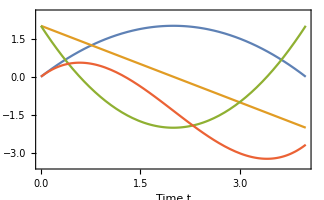

```mathematica
g=1;T=4;
Plot[{xt,vt,Lt,St}//Evaluate,{t,0,T},
FrameLabel->"Time t",
PlotLegends->{"Position x","Velocity v","Lagrangian L","Action S"},PlotRange->{-3.5,2.5},PlotRangePadding->0]
```

#### Multiple bounces

```mathematica
findFoci[xi_,vi_,T_,g_]:=Module[{vm,n,k0Floor,tF,xF,t0,tb,tFxFk},
vm=√(vi^2+2g xi);k0Floor=Floor[1/2(1-vm/vi)];n=⌈(g T-vi)/(2vm)⌉;
t0=vi/g;tb=(2vm)/g;
tFxFk={};
Do[        
If[k==k0Floor,Continue[]];
tF=(2k)/g(vi^2+2k vi vm+vm^2)/(2k vi+vm);
xF=(vm^2/(2g)-g/2(tF-t0-tb Floor[(tF-t0)/tb+1/2])^2);
If[tF>T,Continue[]];
AppendTo[tFxFk,{tF,xF}];
,{k,n}];
Return[tFxFk];
];
```

```mathematica
mt[T_]:=Module[{vm,n,j,k,m},  (* find number of foci  *)
vm=√(vi^2+2 g xi);
n=Floor[(g T-vi)/(2vm)+1/2];(* number of bounces *)
j=Floor[(g T-vi)/(2vm)]+UnitStep[vi];(* index n of strip [region between bounces] in which (T,vi) is located *)
k=j+UnitStep[-√(g xi)-vi √(2j(j+1))];
m=j+UnitStep[T-(2k)/g(vi^2+2k vi vm+vm^2)/(2k vi+vm)]+2n; (* note the n *)
Return[m]];
```

```mathematica
xi=2;vi=4;T=20;
M=g=ℏ=1;
vm=√(vi^2+2 g xi);τ=(2 vm)/g;t0=vi/g;
Clear[t,xt,vt,Lt,St];
xt[t_]=vm^2/(2 g)-1/2 g (t-t0-τ Floor[(t-t0)/τ+1/2])^2;
vt[t_]=-g (t-t0-τ Floor[(t-t0)/τ+1/2])//FullSimplify;
Lt[t_]=M/2 vt[t]^2-M g xt[t]//FullSimplify;
St[t_]:=Module[{n,vf},n=Floor[(t-t0)/τ+1/2];vf=vi-g t+2n vm;M/(6g)(2(vi^3-vf^3)-3 vm^2(vi-vf)-2n vm^3)];
θt[t_]:=1/ℏ St[t]-mt[t] π/2;
tFxFk=findFoci[xi,vi,T,g]//N;
```

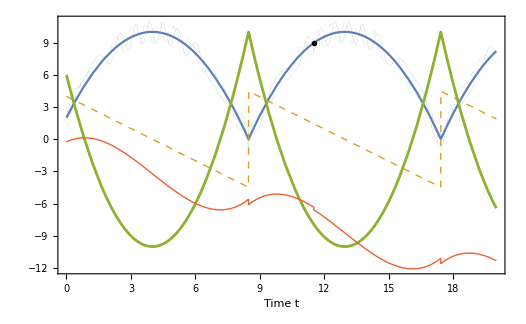

```mathematica
Plot[{xt[t],vt[t],Lt[t],θt[t]/(2π),xt[t]+1*Cos[θt[t]],xt[t]+1*Sin[θt[t]]},{t,0,T},
PlotStyle->{
ColorData[97]@1,
{AbsoluteThickness@1,Dashed,ColorData[97]@2},
{AbsoluteThickness@2,ColorData[97]@3},
{AbsoluteThickness@1,ColorData[97]@4},
{AbsoluteThickness@0,ColorData[97]@1},
{AbsoluteThickness@0,Dashed,ColorData[97]@1}},
Epilog->{Inset[Graphics[{Blue,AbsoluteThickness@2,gpStar}],#,{0,0},Scaled@.05]&/@tFxFk},
Exclusions->None,Frame->True,FrameLabel->{"Time t"},RotateLabel->True,
PlotLegends->{"Position x","Velocity v","Lagrangian L","Phase TraditionalForm`θ" },
ImageSize->{526,324},AspectRatio->Full,
PlotRange->All,PlotRangePadding->{0,Scaled@.05},AxesOrigin->{0,0},
ImagePadding->{{Automatic,Automatic},{Automatic,4}}
]
```

In the plot above, the orange curve shows that θ(t) jumps by -π at bounces, and θ(t) jumps by -π/2 at foci.  It would be nice to somehow show this “on top” of the blue path x(t), but I don’t know how.

### Section.Subsection Phase diagram as function of (x_f,T) for fixed x_i: obtaining caustics as loci of foci

Plotting many paths by brute force reveals that the paths overlap strongly along caustic curves:

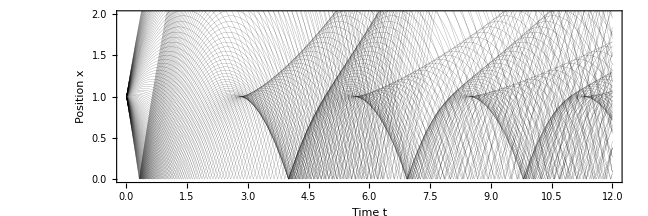

```mathematica
xi=1;   (* initial position *)
g=1;     (* gravitational field strength *)
viList=Range[-3,3,.05];  (* list of initial velocities for plotting *)
Tmax=12; (* maximum time for plotting *)
xmax=2; (* maximum position for plotting *)
plotPathVi[xi_,vi_,T_,g_,style_:Directive[AbsoluteThickness@0,Opacity[0.25,Black]] ]:=Module[{vm,xt,tb,t0,αmax,colorα},
vm=√(vi^2+2g xi);t0=vi/g;tb=(2vm)/g;     (* vm and tb are lists *)
xt=Function[{t},vm^2/(2g)-g/2(t-t0-tb Floor[(t-t0)/tb+1/2])^2];
Plot[Evaluate[xt[t]],{t,0,T},PlotStyle->style,Exclusions->None]];
gr=Show[
Table[    plotPathVi[xi,vi,Tmax,g,Directive[AbsoluteThickness@0.1,Black]]    ,{vi,viList}],
Frame->True,FrameLabel->{"Time t","Position x"},RotateLabel->True,
PlotRange->{{0,Tmax},{0,xmax}},PlotRangePadding->0,
ImageSize->{648,216},AspectRatio->Full,ImagePadding->{{Automatic,Automatic},{Automatic,8}}]
```

From our analysis of the symmetric bouncer, we find that for a path with initial position x_i, initial velocity v_i, and k bounces, there is a focus at time
	t_k^F=(2k)/g(v_i^2+2k v_i v_m+v_m^2)/(2k v_i+v_m)=(2k)/g(2 v_i^2+2g x_i+2k v_i √(v_i^2+2g x_i))/(2k v_i+√(v_i^2+2g x_i)).
The position at this time is
	x_k^F=X(t_k^F)	where X(t)=x_i+v_i^2/(2g)-g/2(t-v_i/g-(2 √(v_i^2+2g x_i))/g k)^2.	
If we loop over each value of k=1,2,3,…, loop over many values of v_i, and make a ParametricPlot of the locus of (t_k^F,x_k^F), we obtain the caustics.  The caustics are the loci of the foci.

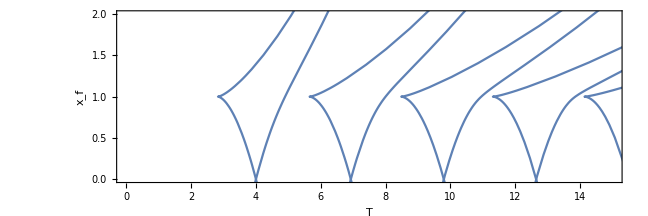

```mathematica
Clear[n,vi,xi,g];
xi=1;g=1;
ParametricPlot[
Table[{
(2n)/g*(2 vi^2+2g xi+2n vi √(vi^2+2g xi))/(√(vi^2+2g xi)+2n vi),
xi+vi^2/(2g)-g/2((2n)/g*(2 vi^2+2g xi+2n vi √(vi^2+2g xi))/(√(vi^2+2g xi)+2n vi)-vi/g-(2 √(vi^2+2g xi))/g n)^2
},{n,1,6}]
,{vi,-5,5},PlotRange->{{0,15},{0,2}},ImageSize->{648,216},AspectRatio->Full,
FrameLabel->{"T","x_f"}]
```

The pattern of caustics above is universal.  Changing x_f merely results in rescaling.

### Section.Subsection Phase diagram as function of (x_f,T) for fixed x_i: discriminant method

#### Crude method

```mathematica
nPaths[xf_,xi_,T_,M_,g_,ℏ_]:=Module[{uSols,vi,n,nmax,a,b,vm,vf,S,k,u,v,w,dSdxidxf},
a=(2xi)/(g T^2);b=(2xf)/(g T^2);nmax=Ceiling[√(1+1/(2a+2b))];(*-------- n,u,v,w,vi,S,dSdxidxf ARE LISTS --------*)
{n,u}=Do[
uSols=Which[
n==0,{(1+b-a)/2},
n==1,Root[1-10 a+9 a^2+2 b+6 a b+b^2+(-4+20 a-4 b) #1+(-4+8 a+8 b) #1^2+16 #1^3&,#]&/@Range@3,
True,Root[16(n^4-n^2)#^4+16 n^2#^3+(32 n^4 a+8 n^2(b-1-3a)+4)#^2+4(4 n^2 a+a-b-1)#+(16 n^4 a^2+8 n^2 a(b-1-a)+(1+b-a)^2)&,#]&/@Range@4
]//N//Union//Select[#,Im[#]==0&]&;
Sow/@{{n,#}}&/@uSols;
,{n,0,nmax}]//Reap//Last//Last//Transpose;
Length@u
];
```

```mathematica
(*-------- USER-DEFINED PARAMETERS --------*)
xi=10;
xfList=Range[0.0625,15.0,8* 0.0625]; (* position grid *)
TList=Range[0.03125,25,8 *.03125];
Monitor[timeIt[   data=Table[nPaths[xf,xi,T,1,1,1],{T,TList},{xf,xfList}]    ],{T,xf}];
```

Absolute time = 4.33    CPU time = 4.29

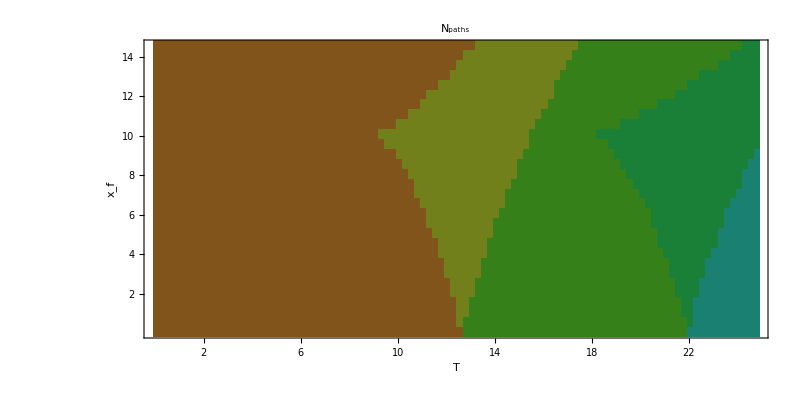

```mathematica
gr=myComplexPlot[TList,xfList,Exp[.3I data],FrameLabel->Reverse@{"T","x_f"},PlotLabel->"N_paths",ImageSize->{800,400}]
```

#### Plot phase diagram

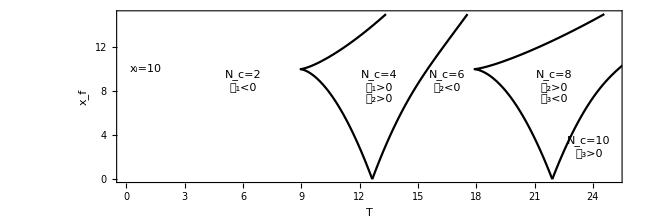

```mathematica
xi=10;
xmax=15;
Clear[findT];    (*---- assume g=1 ----*)
findT[xi_,xf_,1,1]:=Sqrt@Root[-64 xf^3-192 xf^2 xi-192 xf xi^2-64 xi^3+(-60 xf^2+312 xf xi-60 xi^2) #1+(-12 xf-12 xi) #1^2+#1^3&,1];
findT[xi_,xf_,n_,nroot_]:=Sqrt@
Root[-256 n^2 xf^4+256 n^4 xf^4+1024 n^2 xf^3 xi-3072 n^4 xf^3 xi+2048 n^6 xf^3 xi-1536 n^2 xf^2 xi^2+5632 n^4 xf^2 xi^2-8192 n^6 xf^2 xi^2+4096 n^8 xf^2 xi^2+1024 n^2 xf xi^3-3072 n^4 xf xi^3+2048 n^6 xf xi^3-256 n^2 xi^4+256 n^4 xi^4+(-320 n^2 xf^3+256 n^4 xf^3+320 n^2 xf^2 xi+512 n^4 xf^2 xi-1024 n^6 xf^2 xi+320 n^2 xf xi^2+512 n^4 xf xi^2-1024 n^6 xf xi^2-320 n^2 xi^3+256 n^4 xi^3) #1+(4 xf^2-128 n^2 xf^2+64 n^4 xf^2-8 xf xi+64 n^2 xf xi+256 n^4 xf xi+4 xi^2-128 n^2 xi^2+64 n^4 xi^2) #1^2+(4 xf-16 n^2 xf+4 xi-16 n^2 xi) #1^3+#1^4&,nroot];
grPD=ParametricPlot[{
{findT[xi,xf,1,1],xf},
{findT[xi,xf,2,1],xf},
{findT[xi,xf,2,2],xf},
{findT[xi,xf,3,1],xf},
{findT[xi,xf,3,2],xf}
},{xf,0,xmax},
PlotRange->{{0,25},{0,15}},PlotRangePadding->0,PlotStyle->Black,
ImageSize->{648,216},AspectRatio->Full,FrameLabel->{"T","x_f"},
ImagePadding->{{Automatic,Automatic},{Automatic,4}},
Epilog->{
{
Text["N_c=2\n𝒟_1<0",{6,10},{0,1}],
Text["N_c=4\n𝒟_1>0\n𝒟_2>0",{13,10},{0,1}],
Text["N_c=6\n𝒟_2<0",{16.5,10},{0,1}],
Text["N_c=8\n𝒟_2>0\n𝒟_3<0",{22,10},{0,1}],
Text["N_c=10\n𝒟_3>0",{23.8,4},{0,1}]
}//Style[#,16]&,
Text["x_i=10",{1,xi}]
}]
```

### Section.Subsection Phase diagram as function of (x_i,x_f) for fixed T – a bit old

(Warning: here a and b are different from their definitions in the paper.)

In this section, we analyze the quartic equation to obtain the number of physically meaningful solutions.  Examine the discriminant:

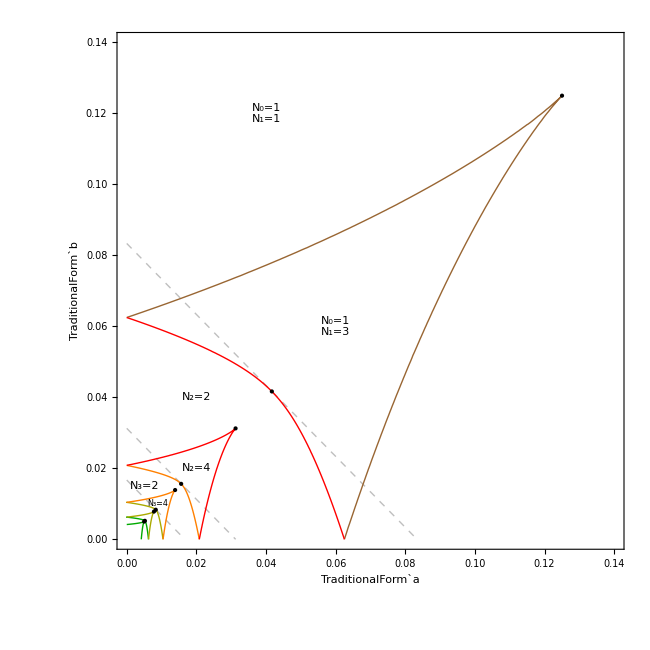

```mathematica
Clear[a,b,n,u,discrim4];
discrim[n_,a_,b_]=Discriminant[1-4 a+4 a^2+4 b-8 a b+4 b^2-16 a n^2-32 a^2 n^2+32 a b n^2+64 a^2 n^4+(-4+8 a-8 b+32 a n^2) u+(4-8 n^2-48 a n^2+16 b n^2+64 a n^4) u^2+16 n^2 u^3+(-16 n^2+16 n^4) u^4,u]/65536;
cpOpts={PlotRange->All,ContourShading->None,MaxRecursion->3};
gr=Show[
(*-------- DASHED LINES: STRAIGHT LINE APPROXIMATION --------*)
ContourPlot[√(1+1/(4(a+b))),{a,0,.2},{b,0,.2},Contours->{1,2,3,4},ContourStyle->{{Dashed,GrayLevel@.75}},cpOpts//Evaluate],
(*-------- ZERO CONTOURS OF DISCRIMINANTS FOR n=1,2,3,4,5 --------*)
ContourPlot[discrim[1,a,b],{a,0,1/8},{b,0,1/8},Contours->{0},ContourStyle->resistorColorList⟦2⟧,cpOpts//Evaluate],
Table[
ContourPlot[discrim[n,a,b],{a,0,1/(8n(n-1))},{b,0,1/(8n(n-1))},Contours->{0},ContourStyle->resistorColorList⟦1+n⟧,cpOpts//Evaluate]
,{n,{5,4,3,2}}],
(*-------- OTHER ANNOTATIONS --------*)
Graphics[{AbsolutePointSize@3,Table[Point@{1/(8 n^2),1/(8 n^2)},{n,1,5}],Table[Point@{1/(8(n^2-1)),1/(8(n^2-1))},{n,2,5}],
Text["N_0=1\nN_1=1",{.04,.12}],Text["N_0=1\nN_1=3",{.06,.06}],Text["N_2=2",{.02,.04}],
Text["N_2=4",{.02,.02}],Text["N_3=2",{.005,.015}],Text["N_3=4"//Style[#,8]&,{.009,.01}]
}//Style[#,FontFamily->"Times"]&],
PlotRange->{{0,1},{0,1}}*0.14,RotateLabel->False,LabelStyle->{Black,12,FontFamily->"Times"},PlotRangePadding->0,
ImageSize->650,
FrameLabel->{"TraditionalForm`a","TraditionalForm`b"}]//
Legended[#,Placed[#,{.9,.5}]&@LineLegend[Rest@resistorColorList,{"D_1=0","D_2=0","D_3=0","D_4=0"},LabelStyle->{Black,14,FontFamily->"Times"}]]&
```

Number of parameters:  The classical bouncer has only two dimensionless parameters, which are the scaled initial and final altitudes a and b.

Discriminant study:  The figure above shows zero contours of the discriminant of the quartic polynomial in the equation for the initial velocity v_i=ugT as a function of the initial altitude x_i=ag T^2 and final altitude x_f=bg T^2, for various values of n (the number of bounces).  The regions of the phase diagram are labeled with the numbers of paths for the largest number of bounces.  For example, in the region labeled “N_3=2”, the path counts are N_0=1 (one direct path), N_1=3 (three single-bounce paths), N_2=4 (four double-bounce paths), and N_3=2 (two triple-bounce paths).

Existence of solutions for n=0 and n=1
It is always possible to find a direct path from x_i to x_f in time T with zero bounces, by throwing the ball up into the air.
It is always possible to find a path from x_i to x_f in time T with one bounce, by throwing the ball against the ground.
For large values of x_i and x_f, these are the only two solutions.

Extra solutions
As x_i and x_f are reduced (or as T increases), the number of possible paths increases.  Every time the discriminant of a polynomial crosses zero, the number of roots of that polynomial increases by two.  For example, to the bottom left of the brown curve, there are three single-bounce solutions with n=1.  Going further to the bottom left, two double-bounce solutions appear, followed by two more to make a total of four double-bounce solutions.  The pattern appears roughly self-similar.

To get more insight, consider symmetrical trajectories where x_i=x_f, that is, a=b.  The discriminant simplifies to D=65536 n^4 ((8a n^2-1)^3 [(4+8a)n^2-1])^2 [8a(n^2-1)-1].  For a given value of n, D is a sixth-degree polynomial in a.  D changes sign at a=1/8 n^2 and also at a=1/8(n^2-1).  Thus, for a given value of n, solutions are possible for a≤1/8(n^2-1).  Conversely, for a given value of a, the allowed values of n satisfy n≤√(1+1/8a).  Thus an upper bound on n is n_max=⌈√(1+1/8a)⌉.  Returning to the general case where a≠b, we can construct the tangent to the boundaries by replacing a by (a+b)/2.  This gives us a general upper bound as n_max=⌈√(1+1/4(a+b))⌉.  These lines are the light gray dashed lines in the phase diagram above.

Heuristic arguments
Suppose the initial and final heights x_i and x_f are given, and suppose x_i≥x_f for concreteness.  The overall motion of the particle is slowest if the total energy is as small as possible, in other words, if the particle starts at rest with v_i=0.  Then:
– the duration of the first segment of the trajectory is t_1=√(2x_i/g)
– the time interval between bounces is Δ t_min=√(8x_i/g)
– the duration of the last segment of the trajectory, T-t_n, is between 0 and √(8x_i/g).
In this case, the total time elapsed is T≥√(2x_i/g)+(n-1)√(8x_i/g), that is, T≥(2n-1)√(2x_i/g).  So the number of bounces satisfies n≤T √(g/(8 x_i))+1/2.  If the initial velocity is v_i≠0, then the time between bounces is Δt=(2 √(v_i^2+2g x_i))/g>√(8x_i/g).  It is possible that this increases the number of bounces by 1, but asymptotically, increasing initial speed will reduce the total number of bounces.  In any case, taking T≥(2n-1)√(2x_i/g) and writing x_i=ag T^2, we see that 8 n^2 a<1 (roughly), in agreement with the rigorous bounds derived earlier on.

Summary
If a particle goes from height x_i to height x_f in time T, the maximum number of bounces cannot exceed
	n_max=⌈√(1+1/(4(a+b)))⌉. 
Also, since there are at most four trajectories for each value of n, the maximum number of paths cannot exceed
	N_max=4+4⌈√(1+1/(4(a+b)))⌉.

This means that calculating the propagator of the quantum bouncer using the Feynman path integral should involve a sum over a finite number of paths!  This is in marked contrast to the case of the classical particle-in-a-box bouncing between two hard walls, where there are an infinite number of possible paths.  To calculate the propagator of the particle-in-a-box using the FPI requires an infinite sum (over an infinite number of “images”)!

### Section.Subsection Van Vleck determinant D_α – details of derivation

#### Calculating (∂v_i)/(∂x_i), (∂v_i)/(∂x_f), and (∂^2 S)/(∂x_i∂x_f)

Equation for v_i:  In the section on “Relation between time of flight T and initial velocity v_i” we showed that
	2k(u-1)√(u^2+a)+k^2 u^2-2u+(k^2-1)a+b+1=0.

Equations for (∂v_i)/(∂x_i) and (∂v_i)/(∂x_f):  Starting with the equation above, perform implicit differentiation, assuming that k is a constant.  We obtain
	2k[du √(u^2+a)+(u-1)(1/2(2u du+da)/(√(u^2+a)))]+(2 k^2 u-2)du+(k^2-1)da+db=0
∴	2k √(u^2+a)du+(2ku(u-1) du)/(√(u^2+a))+(k(u-1) da)/(√(u^2+a))+(2 k^2 u-2)du+(k^2-1)da+db=0
∴	[2k √(u^2+a)+(2ku(u-1))/(√(u^2+a))+2 k^2 u-2]du+[(k(u-1))/(√(u^2+a))+k^2-1]da+db=0
∴	(∂u)/(∂a)=-[(k(u-1))/(√(u^2+a))+k^2-1]/[2k √(u^2+a)+(2ku(u-1))/(√(u^2+a))+2 k^2 u-2]
 	(∂u)/(∂b)=-1/[2k √(u^2+a)+(2ku(u-1))/(√(u^2+a))+2 k^2 u-2].
If desired, we can redimensionalize to obtain (∂v_i)/(∂x_i)=2/T(∂u)/(∂a) and (∂v_f)/(∂x_f)=2/T(∂u)/(∂b).

The van Vleck determinant (∂^2 S)/(∂x_i∂x_f):  Recall that the action for the multi-bounce path may be written as S(a,u) where
	S=(M g^2 T^3)/6[2+3a-24a n^2-6u+24a n^2 u+3 u^2+24 n^2 u^2-24 n^2 u^3+(-12n-4an+16a n^3+24nu-8n u^2-16 n^3 u^2) √(u^2+a)].
Treat g, T, and n as constants.  We want to compute |det (∂^2 S)/(∂x_i∂x_f)|.  Since we have a 1D problem, this is just |(∂^2 S)/(∂x_i∂x_f)|.  Using the chain rule,
	(∂S(a,b))/(∂a)=(∂S(a,u))/(∂a)+(∂u)/(∂a)(∂S(a,u))/(∂u)=^def f(a,u).
Differentiate this further with respect to b:
	(∂^2 S)/(∂a∂b)=∂/(∂b)f=(∂u)/(∂b)(∂f)/(∂u).
In this way we obtain a closed-form expression for (∂^2 S)/(∂a∂b) as a function of a and u.  After much manipulation,
	(∂^2 S)/(∂x_i∂x_f)=4/(g^2 T^4)(∂^2 S)/(∂a∂b)
		=M/T w/(2n(a-u)+4n u^2-w+4 n^2 uw) 	where w=√(u^2+a)
		=M/T w^2/(uv+av-bu)				in terms of x_i,x_f,v_i,v_f,v_m
		=M/T(1-u+v)^2/(4 n^2 (uv+av-bu))			in terms of x_i,x_f,v_i,v_f,n
		=M/T w^2/(uv(1+v-u)+(v-u)w^2)		in terms of v_i,v_f,v_m
		=M/T(v-u+1)/(u^2+v^2+v-u+(4 n^2-2)uv)		in terms of v_i,v_f,n.
We have used the relations v=u-1+2nw and w^2=u^2+a=v^2+b above.  We will not write (∂^2 S)/(∂x_i∂x_f) in terms of x_i,x_f,T alone because of the sign ambiguity problem.

Close to a stationary path,
	(∂^2 S)/(∂x_i∂x_f)(v_i,v_f,v_m)=(M v_m^2)/(T v_i v_f+2(x_i v_f-x_f v_i)).

#### Mathematica derivation of (∂v_i)/(∂x_i) and (∂v_i)/(∂x_f)

```mathematica
(*-------- FULLY AUTOMATIC CALCULATION --------*)
2k(u-1)√(u^2+a)+k^2 u^2-2u+(k^2-1)a+b+1        /.{u->u[z],a->a[z],b->b[z]}
D[(%), z] //FullSimplify
dLHS=% /.{a'[z]->da,b'[z]->db,u'[z]->du,a[z]->a,b[z]->b,u[z]->u}
duda=Solve[dLHS==0/.{db->0,da->1},du]//Last//Last//Last//FullSimplify
dudb=Solve[dLHS==0/.{db->1,da->0},du]//Last//Last//Last//FullSimplify
```

1+(-1+k^2) a[z]+b[z]-2 u[z]+k^2 u[z]^2+2 k (-1+u[z]) √(a[z]+u[z]^2)

(-1+k^2) a'[z]+b'[z]-2 u'[z]+2 k^2 u[z] u'[z]+2 k √(a[z]+u[z]^2) u'[z]+(k (-1+u[z]) (a'[z]+2 u[z] u'[z]))/(√(a[z]+u[z]^2))

db-2 du+da (-1+k^2)+2 du k^2 u+(k (-1+u) (da+2 du u))/(√(a+u^2))+2 du k √(a+u^2)

(√(a+u^2)-k (-1+u+k √(a+u^2)))/(2 (a k-√(a+u^2)+k u (-1+2 u+k √(a+u^2))))

-(√(a+u^2))/(2 (a k-√(a+u^2)+k u (-1+2 u+k √(a+u^2))))

```mathematica
blah=duda/.√(a+u^2)->w//FullSimplify;
num=blah//Numerator//Expand;
den=blah//Denominator//Expand;
dudaCollected=(num//Collect[#,w]&)/(den//Collect[#,w]&)/.w->√(a+u^2)
dudaCollected-duda//FullSimplify
(*(num*(den/.w->-w)//Expand//(#/.w^2->u^2+a&)//FullSimplify//Collect[#,w]&)/(den*(den/.w->-w)//Expand//(#/.w^2->u^2+a&)//FullSimplify//Collect[#,w]&)/.w->√(a+u^2)//FullSimplify*)
```

(k-k u+(1-k^2) √(a+u^2))/(2 a k-2 k u+4 k u^2+(-2+2 k^2 u) √(a+u^2))

0

```mathematica
blah=dudb/.√(a+u^2)->w//FullSimplify;
num=blah//Numerator//Expand;
den=blah//Denominator//Expand;
dudbCollected=(num//Collect[#,w]&)/(den//Collect[#,w]&)/.w->√(a+u^2)
dudbCollected-dudb//FullSimplify
```

-(√(a+u^2))/(2 a k-2 k u+4 k u^2+(-2+2 k^2 u) √(a+u^2))

0

```mathematica
(*-------- MANUAL ENTERING --------*)
dudaManual=-((k(u-1))/(√(u^2+a))+k^2-1)/(2k √(u^2+a)+(2k u(u-1))/(√(u^2+a))+2 k^2 u-2)//FullSimplify
```

-(-1+k^2+(k (-1+u))/(√(a+u^2)))/(2 (-1+k^2 u+(k (a+u (-1+2 u)))/(√(a+u^2))))

Check that these are the same:

```mathematica
duda-dudaManual//FullSimplify
```

0

#### Mathematica derivation of (∂^2 S)/(∂x_i∂x_f)

```mathematica
Clear[a,b,g,T,xi,xf,vi,vf,vm,u,v,w,n,M];
SSS=M/(6g)(2(vi^3-vf^3)-3 vm^2(vi-vf)-2n vm^3)/.{vf->vi-g T+2n vm}//FullSimplify;
SSS=SSS/.{vm->√(vi^2+2g xi),vf->√(vi^2+2g (xi-xf))}//FullSimplify;
SSS=SSS/.{xi->a(g T^2)/2,xf->b(g T^2)/2,vi->u g T}//FullSimplify//PowerExpand//FullSimplify
```

-1/6 g^2 M T^3 (-2+3 a (1+8 n^2 (-1+u))+3 u (2+(-1+8 n^2 (-1+u)) u)+4 n √(a+u^2) (3+a (-1+4 n^2)+2 u (-3+u+2 n^2 u)))

```mathematica
duda=(√(a+u^2)-k (-1+u+k √(a+u^2)))/(2 (a k-√(a+u^2)+k u (-1+2 u+k √(a+u^2))))/.k->2n//FullSimplify
dudb=-(√(a+u^2))/(2 (a k-√(a+u^2)+k u (-1+2 u+k √(a+u^2))))/.k->2n//FullSimplify
dSda=D[SSS, a]+duda*D[SSS, u]//Simplify
dSdbda=dudb*D[dSda, u]//Simplify
dSdxidxf=4/(g^2 T^4)dSdbda//FullSimplify
```

(√(a+u^2)-2 n (-1+u+2 n √(a+u^2)))/(-2 √(a+u^2)+4 n (a+u (-1+2 u+2 n √(a+u^2))))

-(√(a+u^2))/(-2 √(a+u^2)+4 n (a+u (-1+2 u+2 n √(a+u^2))))

-1/2 g^2 M T^3 u

(g^2 M T^3 √(a+u^2))/(2 (-2 √(a+u^2)+4 n (a+u (-1+2 u+2 n √(a+u^2)))))

(M √(a+u^2))/(T (-√(a+u^2)+2 n (a+u (-1+2 u+2 n √(a+u^2)))))

```mathematica
T/M dSdxidxf/.{n->(v-u+1)/(2w)}/.{u->√(w^2-a),v->√(w^2-b)}//Simplify//PowerExpand//FullSimplify
%/.{√(w^2-a)->u,√(w^2-b)->v}//Factor
```

w^2/(-b √(-a+w^2)+√(-b+w^2) (a+√(-a+w^2)))

-w^2/(b u-a v-u v)

```mathematica
-w^2/(b u-a v-u v)/.w->(v-u+1)/(2n)//FullSimplify
```

-(1-u+v)^2/(4 n^2 (b u-(a+u) v))

#### Numerical verification

```mathematica
calc˘vi˘n[xf_,xi_,T_,M_,g_,ℏ_]:=Module[{t,t1,Δt,tn,a,b,n,vi,vm,vf,uSols,nα,uα,αmax,nmax,Sα,S},
a=(2xi)/(g T^2);b=(2xf)/(g T^2);nmax=Ceiling[√(1+1/(2a+2b))];
{nα,uα}=Do[
uSols=Which[
n==0,{(1+b-a)/2},
n==1,Root[1-10 a+9 a^2+2 b+6 a b+b^2+(-4+20 a-4 b) #1+(-4+8 a+8 b) #1^2+16 #1^3&,#]&/@Range@3,
True,Root[16(n^4-n^2)#^4+16 n^2#^3+(32 n^4 a+8 n^2(b-1-3a)+4)#^2+4(4 n^2 a+a-b-1)#+(16 n^4 a^2+8 n^2 a(b-1-a)+(1+b-a)^2)&,#]&/@Range@4
]//N//Union//Select[#,Im[#]==0&]&;
Sow/@{{n,#}}&/@uSols;
,{n,0,nmax}]//Reap//Last//Last//Transpose;
{uα*g*T,nα}
];
calc˘vi[xf_,xi_,T_,M_,g_,ℏ_]:=Module[{vi,n},
{vi,n}=calc˘vi˘n[xf,xi,T,M,g,ℏ];
vi
];
calc˘dvidxi[xf_,xi_,T_,M_,g_,ℏ_]:=Module[{vi,n,u,a,b,k,duda},
{vi,n}=calc˘vi˘n[xf,xi,T,M,g,ℏ];(* note that vi,n,u,vm,vf,S are all vectors *)
u=vi/(g T);a=(2xi)/(g T^2);b=(2xf)/(g T^2);k=2n;duda=(√(a+u^2)-k (-1+u+k √(a+u^2)))/(2 (a k-√(a+u^2)+k u (-1+2 u+k √(a+u^2))));2/T duda
];
calc˘dvidxf[xf_,xi_,T_,M_,g_,ℏ_]:=Module[{vi,n,u,a,b,k,dudb},
{vi,n}=calc˘vi˘n[xf,xi,T,M,g,ℏ];
u=vi/(g T);a=(2xi)/(g T^2);b=(2xf)/(g T^2);k=2n;dudb=-(√(a+u^2))/(2 (a k-√(a+u^2)+k u (-1+2 u+k √(a+u^2))));2/T dudb
];
calc˘S[xf_,xi_,T_,M_,g_,ℏ_]:=Module[{vi,n,vm,vf,S,a,b,u,v,w},
{vi,n}=calc˘vi˘n[xf,xi,T,M,g,ℏ];
a=(2xi)/(g T^2);u=vi/(g T);w=√(u^2+a);v=u-1+2n w;S=(M g^2 T^3)/6(2(u^3-v^3)-3 w^2(u-v)-2n w^3)
];
calc˘dSdxixdf[xf_,xi_,T_,M_,g_,ℏ_]:=Module[{vi,n,k,u,vm,vf,a,b,v,w,dSdxidxf},
{vi,n}=calc˘vi˘n[xf,xi,T,M,g,ℏ];
a=(2xi)/(g T^2);b=(2xf)/(g T^2);u=vi/(g T);w=√(u^2+a);v=u-1+2n w; dSdxidxf=M/T w^2/(u v+a v-b u)
];
```

Do the verification!

```mathematica
xf=1.;xi=2;T=8;M=g=ℏ=1;
Do[Print@((calc˘vi[xf,xi+dx,T,M,g,ℏ]-calc˘vi[xf,xi,T,M,g,ℏ])/dx),{dx,{.1,.01,.001}}]
Print@calc˘dvidxi[xf,xi,T,M,g,ℏ]
```

{-0.125,0.495133,-0.495662,-0.12447,0.594958,-0.591789}

{-0.125,0.490321,-0.490854,-0.124467,0.586627,-0.583417}

{-0.125,0.48985,-0.490383,-0.124467,0.585819,-0.582605}

{-0.125,0.489798,-0.490331,-0.124467,0.585729,-0.582515}

```mathematica
Do[Print@((calc˘vi[xf+dx,xi,T,M,g,ℏ]-calc˘vi[xf,xi,T,M,g,ℏ])/dx),{dx,{.1,.01,.001}}]
Print@calc˘dvidxf[xf,xi,T,M,g,ℏ]
```

{0.125,-0.170977,0.188539,-0.142561,0.222533,-0.293309}

{0.125,-0.171201,0.187855,-0.141654,0.219858,-0.28402}

{0.125,-0.171224,0.187788,-0.141564,0.219596,-0.283144}

{0.125,-0.171226,0.18778,-0.141554,0.219567,-0.283047}

```mathematica
Do[Print@((calc˘S[xf+dx,xi+dx,T,M,g,ℏ]+calc˘S[xf,xi,T,M,g,ℏ]-calc˘S[xf,xi+dx,T,M,g,ℏ]-calc˘S[xf+dx,xi,T,M,g,ℏ])/dx^2),{dx,{.1,.01,.001}}]
Print@calc˘dSdxixdf[xf,xi,T,M,g,ℏ]
```

{-0.125,0.172863,-0.190359,0.142496,-0.22627,0.296301}

{-0.125,0.171387,-0.188035,0.141647,-0.220211,0.28431}

{-0.125,0.171242,-0.187806,0.141563,-0.219632,0.283173}

{-0.125,0.171226,-0.18778,0.141554,-0.219567,0.283047}

## Section Symmetric Bouncer

### Section.Subsection Eigenvalues and eigenfunctions

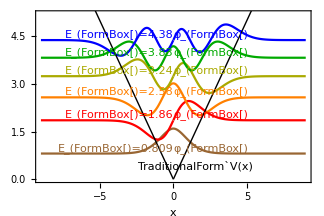

```mathematica
(*======== CLICK ANYWHERE IN THE CODE BELOW AND PRESS SHIFT+ENTER ========*)
nmax=5;
(*-------- CALCULATE AIRY ZEROES AND AIRY PRIME ZEROES --------*)
λn={0}~Join~Table[AiryAiZero[n],{n,nmax}]//N;
μn=Table[Last@Last@FindRoot[AiryAiPrime[x],{x,λn⟦n⟧,λn⟦n+1⟧}],{n,nmax}];
λn=Rest@λn;
(*-------- CALCULATE EIGENENERGIES --------*)
γ=2^(1/3)//N;
EnP=-μn/γ;
EnM=-λn/γ;
En=Riffle[EnP,EnM];
mmax=Length@En;
(*-------- DEFINE EIGENFUNCTIONS --------*)
φmxFunc[m_,x_]:=Module[{n},
If[OddQ[m],
n=(m+1)/2;√(γ/2)1/(√(-μn⟦n⟧)AiryAi[μn⟦n⟧])AiryAi[μn⟦n⟧+γ Abs[x]],
n=m/2;√(γ/2)1/AiryAiPrime[λn⟦n⟧]*AiryAi[λn⟦n⟧+γ Abs[x]]*Sign[x]
]
];
(*-------- PLOT EVERYTHING --------*)
mmax=6;
ymax=5.2;
colors=Rest@resistorColorList;
gr=Show[
Plot[Table[En⟦m⟧+φmxFunc[m,x],{m,1,mmax}]//Evaluate,{x,-9,9},PlotStyle->({#}&/@colors)],
ImageSize->{324,216},AxesOrigin->{0,Automatic},AspectRatio->Full,FrameLabel->{"x",""},
PlotRange->{{-9,9},{0,ymax}},PlotRangePadding->0,
Epilog->{Thick,Line@{{-99,99},{0,0},{99,99}},
Table[{colors⟦n⟧,
Text[StringForm["E_(``)=``",n,En⟦n⟧//N//NumberForm[#,3]&],Scaled[{+.5,0},{0,En⟦n⟧}],{+1.3,-1.2}],
Text[StringForm["φ_(``)",n],Scaled[{-.5,0},{0,En⟦n⟧}],{-2,-1.2}]
},{n,mmax}],
Text["TraditionalForm`V(x)",{1.5,.4}]}
]
```

### Section.Subsection Feynman path integral in semiclassical approximation: infographic

#### Code (run this!)

```mathematica
(*-------- NUMBER OF FOCI BEFORE TIME T --------*)
findMorseIndexM[T_,vi_]:=Module[{vm,j,k,m},
vm=√(vi^2+2 g xi);
(*n=Floor[(g T-vi)/(2vm)+1/2];(* number of bounces *)*)
j=Floor[(g T-vi)/(2vm)]+UnitStep[vi];(* index n of strip [region between bounces] in which (T,vi) is located *)
k=j+UnitStep[-√(g xi)-vi √(2j(j+1))];
m=j+UnitStep[T-(2k)/g(vi^2+2k vi vm+vm^2)/(2k vi+vm)];
Return[m]];

analyze[xi_,xf_,T_,g_]:=Module[{a,b,uSols,kmax,n,viα,u,v,w,SαOverM,DαOverM,mα},
a=(2 Abs@xi)/(g T^2);b=(2Abs@ xf)/(g T^2);kmax=Ceiling[1/2 √(1+1/(2 a+2 b))];
{n,u}=Do[
n=2k+If[xi*xf>0,0,1];
uSols=Which[
n==0,{(1+b-a)/2},
n==1,Root[1-10 a+9 a^2+2 b+6 a b+b^2+(-4+20 a-4 b) #1+(-4+8 a+8 b) #1^2+16 #1^3&,#]&/@Range@3,
True,Root[16(n^4-n^2)#^4+16 n^2#^3+(32 n^4 a+8 n^2(b-1-3a)+4)#^2+4(4 n^2 a+a-b-1)#+(16 n^4 a^2+8 n^2 a(b-1-a)+(1+b-a)^2)&,#]&/@Range@4
]//N//Union//Select[#,Im[#]==0&]&;
Sow/@{{n,#}}&/@uSols;
,{k,0,kmax}]//Reap//Last//Last//Transpose;
viα=u g T;
w=√(u^2+a);v=u-1+2n w;
SαOverM=(g^2 T^3)/6(2(u^3-v^3)-3 w^2(u-v)-2n w^3);
DαOverM=1/T w^2/(u v+a v-b u);
mα=findMorseIndexM[T,#]&/@viα;
{viα,SαOverM,DαOverM,mα}
];

findFoci[xi_,vi_,T_,g_]:=Module[{vm,n,k0Floor,tF,xF,t0,tb,tFxFk},
vm=√(vi^2+2g Abs@xi);k0Floor=Floor[1/2(1-vm/vi)];n=⌈(g T-vi)/(2vm)⌉;
t0=vi/g;tb=(2vm)/g;
tFxFk={};
Do[        
If[k==k0Floor,Continue[]];
tF=(2k)/g(vi^2+2k vi vm+vm^2)/(2k vi+vm);
xF=(vm^2/(2g)-g/2(tF-t0-tb Floor[(tF-t0)/tb+1/2])^2)(-1)^Floor[(tF-t0)/tb+1/2] Sign@xi;
If[tF>T,Continue[]];
AppendTo[tFxFk,{tF,xF}];
,{k,n}];
Return[tFxFk];
];
findXf[xi_,vi_,t_,g_]:=Module[{tb,t0,vm},
vm=√(vi^2+2g Abs@xi);t0=(vi Sign[xi])/g;tb=(2vm)/g;
(vm^2/(2g)-g/2(t-t0-tb Floor[(t-t0)/tb+1/2])^2)(-1)^Floor[(t-t0)/tb+1/2] Sign@xi
];
plotPathVi[xi_,vi_,T_,g_,style_:Directive[AbsoluteThickness@0,Opacity[0.25,Black]] ]:=Module[{vm,xt,tb,t0,αmax,colorα},
vm=√(vi^2+2g Abs@xi);tb=(2vm)/g;t0=(vi Sign@xi)/g;     (* vm and tb are lists; note abs values *)
xt=Function[{t},(vm^2/(2g)-g/2(t-t0-tb Floor[(t-t0)/tb+1/2])^2)(-1)^Floor[(t-t0)/tb+1/2] Sign@xi];
Plot[Evaluate[xt[t]],{t,0,T},PlotStyle->style,Exclusions->None]];
plotPathWithWiggles[xi_,vi_,T_,g_,amp_:0.1,color_:Gray ]:=Module[{vm,xt,St,θt,M=1,ℏ=1,t,tb,t0,αmax,colorα},
vm=√(vi^2+2g Abs@xi);tb=(2vm)/g;t0=(vi Sign@xi)/g;     (* vm and tb are lists; note abs values *)
xt[t_]=(vm^2/(2g)-g/2(t-t0-tb Floor[(t-t0)/tb+1/2])^2)(-1)^Floor[(t-t0)/tb+1/2] Sign@xi;
St[t_]:=Module[{n,vf},n=Floor[(t-t0)/tb+1/2];vf=vi-g t+2n vm;M/(6g)(2(vi^3-vf^3)-3 vm^2(vi-vf)-2n vm^3)];
θt[t_]:=St[t]/ℏ+findMorseIndexM[t,vi];
Plot[{xt[t],xt[t]+amp*Cos[θt[t]](*,xt[t]+amp*Sin[θt[t]]*)},{t,0,T},
PlotStyle->{
{AbsoluteThickness@1,color},
{AbsoluteThickness@2,Lighter[color,.5]},
{AbsoluteThickness@2,CapForm@"Butt",AbsoluteDashing@{1,1},Lighter[color,.5]}},
Exclusions->None]];
```

#### Make the plots

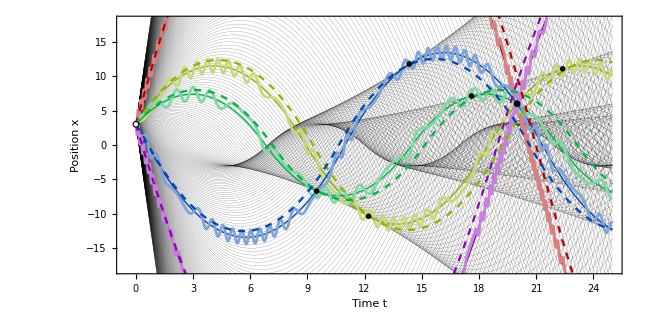
-Graphics-α | v_i^(α) | S_α | D_α | m_α
1 | 10.2 | -423.1 | -0.050 | 1
2 | 4.1 | -71.7 | 0.094 | 2
3 | 3.0 | -61.8 | -0.102 | 3
4 | -4.6 | -95.7 | 0.070 | 2
5 | -9.2 | -247.8 | -0.062 | 1

```mathematica
xi=3;   (* initial position *)
viList=Range[-20,20,.1];  (* list of initial velocities for plotting *)
xf=6;   (* final position *)
T=20;   (* final time *)
g=1;
dvi=0.2; (* perturbation of initial velocity *)
Tmax=25; (* maximum time for plotting *)
xmax=18; (* maximum position for plotting *)
wiggleAmp=1;
(*-------- FIND ALLOWED INITIAL VELOCITIES --------*)
{viα,SαOverM,DαOverM,mα}=Transpose@Reverse@Sort@Transpose@analyze[xi,xf,T,g];
αmax=Length@viα;colorα=Hue[#,1,.7]&/@(Range[0,αmax-1]/αmax)//N;
(*-------- UTILITIES --------*)
gpStar=Line@{{{-1,0},{1,0}},{{0,-1},{0,1}},{{-.71,-.71},{.71,.71}},{{-.71,.71},{.71,-.71}}};
myFrame@gr_:=gr//Framed[#,Background->White]&;
myFrameTranslucent@gr_:=gr//Framed[#,Background->Opacity[.7,White]]&;
myFrame@gr_:=gr//Framed[#,Background->White]&;
myFrameTranslucent@gr_:=gr//Framed[#,Background->Opacity[.7,White]]&;
myLegend=Table[{
α//Style[#,colorα⟦α⟧]&,
viα⟦α⟧//NumberForm[#,{∞,1}]&//Style[#,colorα⟦α⟧]&,(* should multiply by sgn xi *)
SαOverM⟦α⟧//NumberForm[#,{∞,1}]&//Style[#,colorα⟦α⟧]&,
DαOverM⟦α⟧//NumberForm[#,{∞,3}]&//Style[#,colorα⟦α⟧]&,
mα⟦α⟧//Style[#,colorα⟦α⟧]&
},{α,αmax}]//
TableForm[#,TableHeadings->{None,{"α","v_i^(α)","S_α","D_α","m_α"}}]&;
gr=Show[
(*-------- BACKGROUND PATHS --------*)
Table[    plotPathVi[xi,vi,Tmax,g,Directive[AbsoluteThickness@0.1,Black]]    ,{vi,viList}],
(*-------- CLASSICAL PATHS --------*)
(*Table[    plotPathVi[xi,viα⟦α⟧,Tmax,g,colorα⟦α⟧]    ,{α,αmax}],*)
Table[    plotPathWithWiggles[xi,viα⟦α⟧,Tmax,g,wiggleAmp,colorα⟦α⟧]    ,{α,αmax}],
(*-------- PERTURBED PATHS --------*)
Table[    plotPathVi[xi,viα⟦α⟧+dvi,Tmax,g,{Dashed,colorα⟦α⟧}]    ,{α,αmax}],
(*-------- OTHER GRAPHICS --------*)
Graphics[{
(*-------- START AND END POINTS --------*)
Inset[Graphics[{FaceForm[White],EdgeForm@{Thick,Black},Disk[]}],{0,xi},{0,0},Scaled@.05],
Inset[Graphics[{FaceForm[Black],EdgeForm[Black],Disk[]}],{T,xf},{0,0},Scaled@.05]
,
(*-------- FOCI --------*)
Table[
tFxFk=findFoci[xi,viα⟦α⟧,Tmax,g];  (* let's plot all the way*)
Inset[Graphics[{colorα⟦α⟧,AbsoluteThickness@2,gpStar}],#,{0,0},Scaled@.05]&/@tFxFk
  ,{α,αmax}]
}
],
Frame->True,FrameLabel->{"Time t","Position x"},RotateLabel->True,
PlotRange->{{-.5,Tmax},{-xmax,xmax}},PlotRangePadding->0,(*PlotRangeClipping->False,*)
ImageSize->{648,324},AspectRatio->Full,
AxesOrigin->{0,0},
ImagePadding->{{Automatic,Automatic},{Automatic,4}}];
Row@{gr,myLegend}
```

### Section.Subsection Phase diagram as function of (x_f,T) for fixed x_i: discriminant method

```mathematica
Clear[findT];
findT[xi_,xf_,1,1]:=Sqrt@Root[-64 xf^3-192 xf^2 xi-192 xf xi^2-64 xi^3+(-60 xf^2+312 xf xi-60 xi^2) #1+(-12 xf-12 xi) #1^2+#1^3&,1];
findT[xi_,xf_,n_,nroot_]:=Sqrt@
Root[-256 n^2 xf^4+256 n^4 xf^4+1024 n^2 xf^3 xi-3072 n^4 xf^3 xi+2048 n^6 xf^3 xi-1536 n^2 xf^2 xi^2+5632 n^4 xf^2 xi^2-8192 n^6 xf^2 xi^2+4096 n^8 xf^2 xi^2+1024 n^2 xf xi^3-3072 n^4 xf xi^3+2048 n^6 xf xi^3-256 n^2 xi^4+256 n^4 xi^4+(-320 n^2 xf^3+256 n^4 xf^3+320 n^2 xf^2 xi+512 n^4 xf^2 xi-1024 n^6 xf^2 xi+320 n^2 xf xi^2+512 n^4 xf xi^2-1024 n^6 xf xi^2-320 n^2 xi^3+256 n^4 xi^3) #1+(4 xf^2-128 n^2 xf^2+64 n^4 xf^2-8 xf xi+64 n^2 xf xi+256 n^4 xf xi+4 xi^2-128 n^2 xi^2+64 n^4 xi^2) #1^2+(4 xf-16 n^2 xf+4 xi-16 n^2 xi) #1^3+#1^4&,nroot];
plotPhaseDiagram[xi_,Tmax_,xmax_]:=Module[{},
grPD=ParametricPlot[{
{findT[xi,xf,1,1],-xf},
{findT[xi,xf,2,1],xf},
{findT[xi,xf,2,2],xf},
{findT[xi,xf,3,1],-xf},
{findT[xi,xf,3,2],-xf},
{findT[xi,xf,4,1],xf},
{findT[xi,xf,4,2],xf}
},{xf,0,xmax},
PlotRange->{{0,Tmax},{-xmax,xmax}},PlotRangePadding->0,PlotStyle->Black,
ImageSize->{648,216},AspectRatio->Full,FrameLabel->{"T","x_f"},
ImagePadding->{{Automatic,Automatic},{Automatic,4}},
Epilog->{
{
Text["N_c=1",{8,6}],Text["N_c=3",{15,-5}],Text["N_c=5",{22,8}]
}//Style[#,16]&,
Text["x_i=10",{1,xi}]
}]
];
```

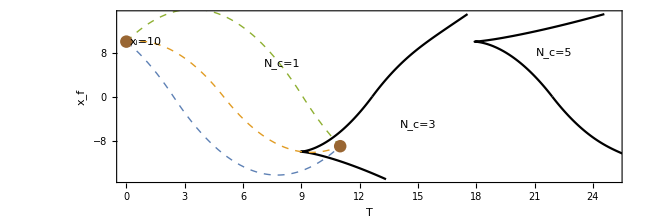

```mathematica
grCombined=Show[
plotPhaseDiagram[10,25,15],
plotPathsXf[10,-9,11,1,1,1,{AbsoluteThickness@1,Dashed}&]
,PlotRangeClipping->True]
```

### Section.Subsection Path divergence function f_α(t) – slightly messy

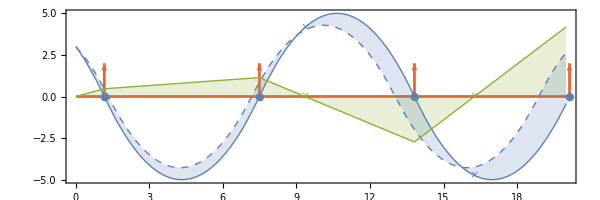

Number of bounces n = 3     Bounce times τ_k = {1.16228,7.48683,13.8114,20.1359}

Number of foci    n_F = 2    Focal times t_k^F = {9.34177,16.258}

```mathematica
(*-------- YOUR CHOICE OF PARAMETERS HERE --------*)
xi=3;vi=-2;dvi=.4;  (* perturbation to initial velocity *)
T=20;g=1;(* these parameters are not important *)
(*-------- CALCULATE INITIAL VELOCITIES --------*)
(*xf=2;viList=findVi[xi,xf,T,1,1,1];vi=First@Nearest[viList,0];Print["vi = ",vi];*)
(*-------- CALCULATE DERIVED PARAMETERS --------*)
tb=(2 √(vi^2+2g Abs@xi))/g;  (* time between bounces *)
t0=(vi Sign@xi)/g;          (* time of zeroth maximum *)
τ1=(vi Sign@xi)/g+tb/2;(* time of first bounce *)
n=⌈(T-τ1)/tb⌉;                   (* number of bounces *)
τk=τ1+(Range[n+1]-1)*tb; (* time of kth bounce *)
(*-------- FIND PATH AND VELOCITY FUNCTIONS --------*)
Clear[t,xt,vt];
xt[t_]=((g tb^2)/8-(g tb^2)/2((t-t0)/tb-Floor[(t-t0)/tb+1/2])^2)(-1)^Floor[(t-t0)/tb+1/2] Sign@xi;
vt[t_]=D[xt[t], t];
xt[t_,xi_,vi_]:=Module[{t0=(vi Sign@xi)/g,tb=(2 √(vi^2+2g Abs@xi))/g},
((g tb^2)/8-(g tb^2)/2((t-t0)/tb-Floor[(t-t0)/tb+1/2])^2)(-1)^Floor[(t-t0)/tb+1/2] Sign@xi
];
(*-------- PATH DIVERGENCE FUNCTION --------*)
ft[T_,vi_]:=Module[{vm,vf,xf,n},(* n is number of bounces before time T *)
vm=√(vi^2+2 g xi);n=Floor[(g T-vi)/(2vm)+1/2];vf=vi-g T+2n vm;xf=vm^2/(2g)-1/(2g)(g T-vi-2n vm)^2;
-(-1)^n(T vi vf+2(xi vf-xf vi))/(M vm^2)];
(*-------- FIND FOCAL TIMES --------*)
vm=√(vi^2+2g Abs@xi);
k0Floor=Floor[1/2(1-vm/vi)];
tFoci=Table[        If[k==k0Floor,{},(2k)/g(vi^2+2k vi vm+vm^2)/(2k vi+vm)],        {k,n}]//Flatten;
(*-------- FIND FOCAL MULTIPLICITY --------*)
nFoci=n-1;
If[1≤k0Floor≤n-1,nFoci-=1];
If[n≠k0Floor&&T>(2n)/g(vi^2+2n vi vm+vm^2)/(2n vi+vm),nFoci+=1];
(*-------- PLOT --------*)
styleX=Directive@{AbsoluteThickness@1,ColorData[97][1]};
styleX2=Directive@{AbsoluteThickness@1,ColorData[97][1],Dashed};
styleVPP=Directive@{AbsoluteThickness@2,ColorData[97][4]};
styleK=Directive@{AbsoluteThickness@2,ColorData[97][4]};
styleF=Directive@{AbsoluteThickness@1,ColorData[97][3]};
myAH=Arrowheads[{{0.02,Automatic,{Graphics[Polygon@{{0,0},{-1,.5},{-1,-.5}}],1}}}];
gr=Plot[{xt[t],xt[t,xi,vi+dvi],dvi*ft[t,vi]},{t,0,T},
PlotStyle->{styleX,styleX2,styleF},Filling->{{1->{2}},3->0},
PlotRange->{{0,T},All},Exclusions->None,
PlotLegends->LineLegend[{
styleX,styleX2,styleK,styleF,White,White},
{"TraditionalForm`X(t)","TraditionalForm`X","κ(t)","f(t) δv_i","bounces (τ_k)","focus (t_k^F)"},
LegendMarkers->{None,None,None,None,Style["●",styleX,16],Style["×",styleX,16,Bold]},
LegendMarkerSize->20
],
ImageSize->{600,200},AspectRatio->Full,
Prolog->{
styleVPP,myAH,Arrow@{{#,0},{#,2}}&/@τk,Line@{{0,0},{T,0}},
styleX,Text["●",{#,0}]&/@τk,
styleF,Text["×",{#,0}]&/@tFoci//Style[#,Bold]&,
styleX,Text["×",{#,xt[#]}]&/@tFoci//Style[#,Bold]&
}]
Print["Number of bounces n = ",n,           "     Bounce times τ_k = ",τk//N];
Print["Number of foci    n_F = ",nFoci,"    Focal times t_k^F = ",tFoci//N]
```

### Section.Subsection Focal times t_k^F – slightly messy

Warning: here u is different from its meaning in the paper.

#### Finding focal times from f_k=-1/2 (-1)^k ((-2+4 k) t0+tb)

```mathematica
Clear[vm,vi,k,g,τk,fk];
fk[k_]:=-1/g(-1)^k(vm+(2k-1)vi);
τk[k_]:=(vi+(2k-1)vm)/g;
tFk=(fk[k+1]*τk[k]-fk[k]*τk[k+1])/(fk[k+1]-fk[k])//FullSimplify
```

```mathematica
Clear[g,xi,vi,k,vm];
(2 k (vi^2+2 k vi vm+vm^2))/(g (2 k vi+vm))/.vm^2->vi^2+2g xi//FullSimplify
```

(4 k (vi^2+k vi vm+g xi))/(g (2 k vi+vm))

Maybe we can do this a different way.  Recall the prescription:
1.  Find v_m=√(v_i^2+2g x_i) and k_0=1/2(1-v_m/v_i).
2.  For k=1,2,3,…,∞, if k≠⌊k_0⌋, then find t_k^F=(2k)/g(v_i^2+2k v_i v_m+v_m^2)/(2k v_i+v_m).
Suppose k=⌊k_0⌋-j=k_c-j.  Then
	t_k^F=(2((k_c-j)))/g(v_i^2+v_m^2+2(k_c-j)v_i v_m)/(2(k_c-j)v_i+v_m).

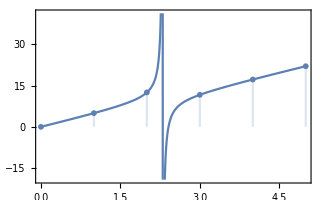

```mathematica
vi=-.5;
vm=2.3;
Show[
Plot[2k*(vi^2+2k vi vm+vm^2)/(2k vi+vm),{k,0,5},PlotRange->Automatic],
DiscretePlot[2k*(vi^2+2k vi vm+vm^2)/(2k vi+vm),{k,0,5},PlotRange->All]
]
```

#### Finding focal times from f(t)=-(-1)^n/M(t v_i v_f+2 x_i v_f-2 x_f v_i)/v_m^2

```mathematica
(*-------- PATH DIVERGENCE FUNCTION --------*) (* n is number of bounces before time T *)
Clear[ft];
ft[t_,vi_]:=Module[{vm,vf,xf,n},
vm=√(vi^2+2 g xi);n=Floor[(g t-vi)/(2vm)+1/2];vf=vi-g t+2n vm;xf=vm^2/(2g)-1/(2g)(g t-vi-2n vm)^2;
(-1)^n(t vi vf+2(xi vf-xf vi))/(M vm^2)];
```

The path divergence function is f(t;x_i,v_i)
	f(t)=-(-1)^n/M(t v_i v_f+2 x_i v_f-2 x_f v_i)/v_m^2
where v_f=v_i-gt+2n v_m and x_f=(v_m^2-v_f^2)/(2g).  The roots occur when
	f(t)=0
∴	t v_i v_f+2 x_i v_f-2 x_f v_i=0
∴	tv_i(v_i-gt+2n v_m)+2x_i(v_i-gt+2n v_m)-2 x_f v_i=0
∴	t=(vi+2 n vm-(vi vm^2)/(vi^2+2 n vi vm+2 g xi))/g
∴	t=1/g(v_i+2n v_m-(v_i v_m)/(v_m+2 n v_i))
∴	t=1/g((v_i+2n v_m)(v_m+2 n v_i)-v_i v_m)/(v_m+2 n v_i)
∴	t=(2n)/g(v_m^2+v_i^2+2n v_i v_m)/(v_m+2n v_i).
This is the same expression as we obtained using the other method.

```mathematica
Clear[xi,vi,M,vm,g,n];
(t vi vf+2(xi vf-xf vi))/(M vm^2)/.xf->(vm^2-vf^2)/(2g)/.{vf->vi-g t+2n vm}//FullSimplify
t vi vf+2(xi vf-xf vi)/.xf->(vm^2-vf^2)/(2g)/.{vf->vi-g t+2n vm}//FullSimplify//Expand
Solve[%==0,t]//FullSimplify
(*%/.vm->√(vi^2+2g xi)*)
```

(vi (vi+vm+2 n vm) (vi+(-1+2 n) vm)-g (vi+2 n vm) (t vi-2 xi)-2 g^2 t xi)/(g M vm^2)

-t vi^2+vi^3/g-2 n t vi vm+(4 n vi^2 vm)/g-(vi vm^2)/g+(4 n^2 vi vm^2)/g-2 g t xi+2 vi xi+4 n vm xi

{{t→(vi+2 n vm-(vi vm^2)/(vi^2+2 n vi vm+2 g xi))/g}}

```mathematica
xi=1;g=1;M=1;
Manipulate[
Plot[ft[t,vi],{t,0,20},PlotRange->9,PlotRangePadding->0,
Epilog->{

}],
{{vi,1},-2,2}]
```

#### Simplified expression for kth focal time

For initial position x_i and initial velocity v_i, plot:
– the time of the kth bounce, τ_k=(v_i+(2k+1)v_m)/g		where v_m=√(v_i^2+2g x_i)
– the time of the kth focus, t_k^F=(2k)/g(v_i^2+2k v_i v_m+v_m^2)/(2k v_i+v_m)	 	provided that k≠⌊1/2(1-v_m/v_i)⌋.

For the purpose of this calculation, to help understand what is going on, take g=1/2 and x_i=1 w.l.o.g. and write v_i=u and v_m=w.  Then......define u=v_i/(√(2g x_i)), and use ???.  Then we have
	t_k^F=2k(2 u^2+1+2ku √(u^2+1))/(√(u^2+1)+2ku) if k<(1-(√(u^2+1))/u)/2-1 or k>(1-(√(u^2+1))/u)/2.
Plotting this, we see that t_k^F consists of two non-connected curves, one for u<-1/(2 √(k^2-k)), and one for u>-1/(2 √(k^2+k)):

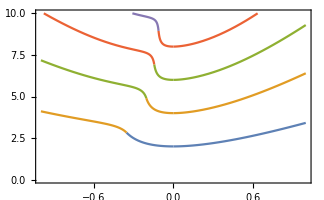

```mathematica
tFuFunc[u_,k_]:=If[-1/2-(√(u^2+1))/(2u)<k<1/2-(√(u^2+1))/(2u),   Indeterminate,2k*(2 u^2+1+2k u √(u^2+1))/(√(u^2+1)+2k u)];
Plot[Table[tFuFunc[u,k],{k,1,5}]//Evaluate,{u,-1,1},PlotRange->{0,10},Exclusions->Automatic]
```

However, the curve of t_k^F (e.g., orange) joins to the curve of t_(k-1)^F (eg., blue).  Let us redefine
	(t̃)_k^F=Piecewise[{{t_(k+1)^F, if u<-1/(2 √(k^2+k))}, {t_k^F, otherwise.}}]
This gives us an expression for the kth focal time that avoids the need to skip over invalid values of k:
	(t̃)_k^F=Piecewise[{{2 (1+k)(1+2 u (u+(1+k) √(1+u^2)))/(2 (1+k) u+√(1+u^2)), if u<-1/(2 √(k^2+k))}, {2k(2 u^2+1+2ku √(u^2+1))/(√(u^2+1)+2ku), otherwise}}]
∴	(t̃)_k^F=2 (1+k)(1+2 u (u+(1+k) √(1+u^2)))/(2 (1+k) u+√(1+u^2))Θ(-1/(2 √(k^2+k))-u)+2k(2 u^2+1+2ku √(u^2+1))/(√(u^2+1)+2ku)Θ(u+1/(2 √(k^2+k))).
Note that a step function may be written as Θ(z)=(z+√(z^2))/(2z).  Thus, in principle, the function (t̃)_k^F(u) may be written entirely in terms of square roots.  I would be very glad if we could find a simpler expression for this function, but I have not been able to.  See graph below for plots.

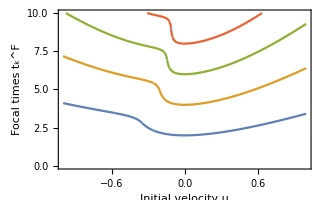

```mathematica
tFuFunc[u_,k_]:=If[u<-1/(2 √(k^2+k)),(2 (1+k) (1+2 u (u+(1+k) √(1+u^2))))/(2 (1+k) u+√(1+u^2)),2k(2 u^2+1+2k u √(u^2+1))/(√(u^2+1)+2k u)];
Plot[Table[tFuFunc[u,k],{k,1,5}]//Evaluate,{u,-1,1},PlotRange->{0,10},Exclusions->Automatic,
FrameLabel->{"Initial velocity u","Focal\ntimes\nt_k^F"}]
```

### Section.Subsection Morse index m as a function of (T,v_i) – slightly messy

This is slightly messy.  Might wish to clean up notation to be consistent with rest of paper.

```mathematica
Clear[tk,τk,u,a,j,k,m,n];
tk[u_,k_]:=u+2k √(u^2+1); (* bounce times *)
(*τk[u_,k_]:=If[-1/2-(√(u^2+1))/(2u)<k<1/2-(√(u^2+1))/(2u),   Indeterminate,2k*(2 u^2+1+2k u √(u^2+1))/(√(u^2+1)+2k u)];(* raw kth focal times *)*)
τk[u_,k_]:=If[u<-1/(√(4k(k+1))), 2(k+1)*(2 u^2+1+2(k+1) u √(u^2+1))/(√(u^2+1)+2(k+1) u),2k*(2 u^2+1+2k u √(u^2+1))/(√(u^2+1)+2k u)];(* kth focal time *)
kFunc[t_,u_]:=Module[{n,k,w,m},  (* code for "zone index" *)
w=√(u^2+1);
(*k=Floor[(t-u-w)/(2w)]+1;(* index of the strip containing the raw kth focal time as in the original defn *)*)
j=Floor[(t-u)/(2w)]+UnitStep[u];(* index of the strip containing the kth focal time? also works *)
Return@j];
mFunc[t_,u_]:=Module[{n,j,k,w,m},  (* code for "Morse index" *)
w=√(u^2+1);
(*k=Floor[(t-u-w)/(2w)]+1;(* index of the strip containing the raw kth focal time as in the original defn *)*)
(*j=Floor[(t-u-w)/(2w)]+UnitStep[u t+1];(* index of the strip containing the kth focal time? *)*)
j=Floor[(t-u)/(2w)]+UnitStep[u];(* index of the strip containing the kth focal time? *)
k=j+UnitStep[-1-√(4j(j+1))u ];
m=j+UnitStep[t-2k(u^2+w^2+2k u w)/(2k u+w)];(* do we include the last focus? *)
Return@m];
```

```mathematica
(*-------- USER-DEFINED PARAMETERS --------*)
xi=1;g=1;
umax=.8;
tList=Range[0.01,15,0.051];
uList=Range[-.8001,.8,0.01]; (* position grid *)
Monitor[timeIt[   kArray=Table[kFunc[T,u],{u,uList},{T,tList}]    ],{T,u}];
Monitor[timeIt[   mArray=Table[mFunc[T,u],{u,uList},{T,tList}]    ],{T,u}];
Dimensions@data
```

Absolute time = 0.58    CPU time = 0.569

Absolute time = 1.71    CPU time = 1.7

{150,81}

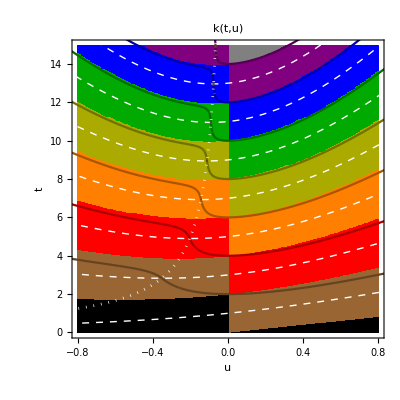
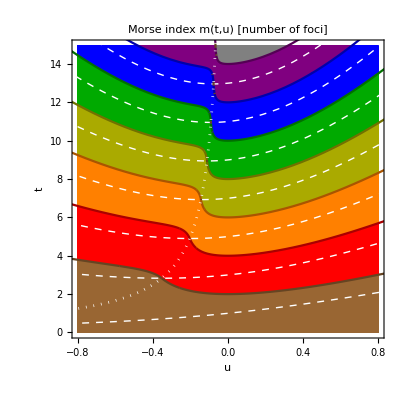

```mathematica
colors=RotateLeft[resistorColorList];
grk=Show[
myIntegerPlot[uList,tList,kArray,FrameLabel->{"t","u"},PlotLabel->"k(t,u)",ImageSize->{400,400},
FrameTicks->{
{autoTicksLabeled[#1,#2,10,.02,.01]&,autoTicksUnlabeled[#1,#2,10,.02,.01]&},
{autoTicksLabeled[#1,#2,10,.006,.003]&,autoTicksUnlabeled[#1,#2,10,.006,.003]&}}],
Plot[Table[tk[u,k-.5],{k,1,7}]//Evaluate,{u,-1,1},PlotStyle->{{Dashed,AbsoluteThickness@1,White}}],(* zenith times *)
Plot[Table[τk[u,k],{k,1,7}]//Evaluate,{u,-1,1},PlotStyle->Darker/@colors,PlotRange->All,Exclusions->Automatic],
Plot[-1/u,{u,-1,0},PlotRange->All,PlotStyle->{{Dotted,AbsoluteThickness@2,White}}]
];
grm=Show[
myIntegerPlot[uList,tList,mArray,FrameLabel->{"t","u"},PlotLabel->"Morse index m(t,u) [number of foci]",ImageSize->{400,400},
FrameTicks->{
{autoTicksLabeled[#1,#2,10,.02,.01]&,autoTicksUnlabeled[#1,#2,10,.02,.01]&},
{autoTicksLabeled[#1,#2,10,.006,.003]&,autoTicksUnlabeled[#1,#2,10,.006,.003]&}}],
Plot[Table[tk[u,k-.5],{k,1,7}]//Evaluate,{u,-1,1},PlotStyle->{{Dashed,AbsoluteThickness@1,White}}],(* zenith times *)
Plot[Table[τk[u,k],{k,1,7}]//Evaluate,{u,-1,1},PlotStyle->Darker/@colors,PlotRange->All,Exclusions->Automatic],
Plot[-1/u,{u,-1,0},PlotRange->All,PlotStyle->{{Dotted,AbsoluteThickness@2,White}}]
];
Row@{grk,grm}
```

Above:  We work in terms of dimensionless variables t̃=?? and u=v_i/(√(2g x_i))  (different from the usual u).    
Dashed white curves are zenith times (t̃)_k.
Dotted white curve is the curve t̃=-1/u.
Colored regions indicate zones (brown=1, red=2, orange=3, etc.)  such that the kth focal time is located within the kth zone.

### Section.Subsection Propagator visualized as heatmap

#### Code: KEE, KPI, KPIAmplitudeOnly

```mathematica
KEE[xfList_,xi_,TList_,M_,g_,ℏ_]:=Module[{nmax,xUnit,EUnit,tUnit},   (* note that xf and T must be lists *)
nmax=10000;
(*-------- TABULATE EIGENVALUES (needs nmax) --------*)
λn={0}~Join~Table[AiryAiZero[n],{n,nmax}]//N;
μn=Table[Last@Last@FindRoot[AiryAiPrime[x],{x,λn⟦n⟧,λn⟦n+1⟧}],{n,nmax}];
λn=Rest@λn;
γ=2^(1/3)//N;
EnP=-μn/γ;EnM=-λn/γ;En=Riffle[EnP,EnM];mmax=Length@En;
(*-------- DEFINE EIGENFUNCTIONS --------*)
φmxFunc[m_,x_]:=Module[{n},
If[OddQ[m],
n=(m+1)/2;√(γ/2)1/(√(-μn⟦n⟧)AiryAi[μn⟦n⟧])AiryAi[μn⟦n⟧+γ Abs[x]],
n=m/2;√(γ/2)1/AiryAiPrime[λn⟦n⟧]*AiryAi[λn⟦n⟧+γ Abs[x]]*Sign[x]
]
];
(*-------- TABULATE DISCRETIZED EIGENFUNCTIONS (needs xfList) --------*)
xj=xfList;
φnjP=√(γ/2)1/(√-μn AiryAi[μn])*Outer[AiryAi[#1+#2]&,μn,γ*Abs[xj]];
φnjM=(Sign[xj]*#&)/@(√(γ/2)1/AiryAiPrime[λn]*Outer[AiryAi[#1+#2]&,λn,γ*Abs[xj]]);
φnj=Riffle[φnjP,φnjM];
(*-------- SET UP TIME EVOLUTION MATRIX (needs TList) --------*)
tPoints=Length@TList;
Unk=Outer[Function[{ε,T},Exp[-I ε T]],En,TList];

cn0=Table[φmxFunc[m,xi],{m,1,mmax}];   (* initial coefficients *)
cnk=cn0*Unk;  (* evolved coefficients *)
KEEData=cnkᵀ.φnj;    (* propagator *)
Return@KEEData
];
```

```mathematica
(*(*-------- CALCULATE MORSE INDEX GIVEN a AND u --------*)
mau[a_,u_]:=Module[{w,j,k,m},
w=√(u^2+a);
j=Floor[(1-u)/(2w)]+UnitStep[u];(* index n of strip [region between bounces] in which (T,vi) is located *)
k=j+UnitStep[-√a-2u √(j(j+1))];
m=j+UnitStep[1-2k(u^2+2k u w+w^2)/(2k u+w)];(* do we include the last focus? *)
Return[m]];*)
```

```mathematica
KPI[xf_,xi_,T_,M_,g_,ℏ_]:=Module[{a,b,kmax,uSols,n,nα,u,v,w,S,dSdxidxf,j,k,m},
a=(2 Abs@xi)/(g T^2);b=(2Abs@ xf)/(g T^2);kmax=Ceiling[1/2 √(1+1/(2 a+2 b))];
{nα,u}=Do[
n=2k+If[xi*xf>0,0,1];
uSols=Which[
n==0,{(1+b-a)/2},
n==1,Root[1-10 a+9 a^2+2 b+6 a b+b^2+(-4+20 a-4 b) #1+(-4+8 a+8 b) #1^2+16 #1^3&,#]&/@Range@3,
True,Root[16(n^4-n^2)#^4+16 n^2#^3+(32 n^4 a+8 n^2(b-1-3a)+4)#^2+4(4 n^2 a+a-b-1)#+(16 n^4 a^2+8 n^2 a(b-1-a)+(1+b-a)^2)&,#]&/@Range@4
]//N//Union//Select[#,Im[#]==0&]&;
Sow/@{{n,#}}&/@uSols;
,{k,0,kmax}]//Reap//Last//Last//Transpose;
w=√(u^2+a);
v=u-1+2nα w;
S=(M g^2 T^3)/6(2(u^3-v^3)-3 w^2(u-v)-2nα w^3);
dSdxidxf=M/T w^2/(u v+a v-b u);
j=Floor[(1-u)/(2w)]+UnitStep[u];(* index n of strip [region between bounces] in which (T,vi) is located *)
k=j+UnitStep[-√a-2u √(j(j+1))];(* this is a different k from before *)
m=j+UnitStep[1-2k(u^2+2k u w+w^2)/(2k u+w)];(* do we include the last focus? *)
Total[√(I/(2π ℏ))√Abs[dSdxidxf]*Exp[(I*S)/ℏ-(I π)/2 m]]
];
```

```mathematica
KPIAmplitudeOnly[xf_,xi_,T_,M_,g_,ℏ_]:=Module[{a,b,kmax,uSols,n,nα,S,dSdxidxf,j,k,m},
a=(2 Abs@xi)/(g T^2);b=(2Abs@ xf)/(g T^2);kmax=Ceiling[1/2 √(1+1/(2 a+2 b))];
{nα,u}=Do[
n=2k+If[xi*xf>0,0,1];
uSols=Which[
n==0,{(1+b-a)/2},
n==1,Root[1-10 a+9 a^2+2 b+6 a b+b^2+(-4+20 a-4 b) #1+(-4+8 a+8 b) #1^2+16 #1^3&,#]&/@Range@3,
True,Root[16(n^4-n^2)#^4+16 n^2#^3+(32 n^4 a+8 n^2(b-1-3a)+4)#^2+4(4 n^2 a+a-b-1)#+(16 n^4 a^2+8 n^2 a(b-1-a)+(1+b-a)^2)&,#]&/@Range@4
]//N//Union//Select[#,Im[#]==0&]&;
Sow/@{{n,#}}&/@uSols;
,{k,0,kmax}]//Reap//Last//Last//Transpose;
w=√(u^2+a);v=u-1+2nα w;
dSdxidxf=M/T w^2/(u v+a v-b u);
Total[√(1/(2π ℏ))√Abs[dSdxidxf]]
];
```

#### Calculate propagator for fixed x_i for various x_f and T

```mathematica
xi=10;
xfList=Range[-15,15,0.0625]; (* fine position grid *)
TList=Range[0.03125,25,0.03125]; (* fine time grid *)
(*xi=10;
xfList=Range[-15,15,8*0.0625]; (* coarse grid *)
TList=Range[0.03125,25,8*0.03125];*)
```

```mathematica
timeIt[
dataKEE=KEE[xfList,xi,TList,1,1,1]        ];
```

Absolute time = 89.2    CPU time = 90.7

```mathematica
Monitor[timeIt[
dataVVD=Table[KPIAmplitudeOnly[xf,xi,T,1,1,1],{T,TList},{xf,xfList}]        ],{T,xf}];
```

Absolute time = 515.    CPU time = 504.

```mathematica
Monitor[timeIt[
dataKPI=Table[KPI[xf,xi,T,1,1,1],{T,TList},{xf,xfList}]        ],{T,xf}];
```

Absolute time = 686.    CPU time = 634.

```mathematica
(*DumpSave[NotebookDirectory[]<>"/bouncer2.mx",{xi,TList,xfList,dataKEE,dataVVD,dataKPI}];*)
```

#### Load data and make graphics

```mathematica
Get[NotebookDirectory[]<>"/bouncer2.mx"];
```

```mathematica
scalFac=1;
grVVD=myComplexPlot[TList,xfList,scalFac*dataVVD,FrameLabel->Reverse@{"T","x_f"},Epilog->{White,Text["K_VVD",Scaled@{0.1,1},{0,1.5}]}];scalFac=2;
grPI=myComplexPlot[TList,xfList,scalFac*dataKPI,FrameLabel->Reverse@{"T","x_f"},Epilog->{White,Text["K_SCA",Scaled@{0.1,1},{0,1.5}]}];
grEE=myComplexPlot[TList,xfList,scalFac*dataKEE,FrameLabel->Reverse@{"T","x_f"},Epilog->{White,Text["K_EE",Scaled@{0.1,1},{0,1.5}]}];
grPIMinusEE=myComplexPlot[TList,xfList,scalFac*(dataKPI- dataKEE),FrameLabel->Reverse@{"T","x_f"},Epilog->{White,Text["K_SCA-K_EE",Scaled@{0.1,1},{0,1.5}]}];
```

```mathematica
gr=YLLGraphicsGrid[
{Reverse@{grVVD,grPI,grEE,grPIMinusEE}}ᵀ,
ColumnSize->600,(* column size(s) *)
RowSize->108,       (* row size(s) *)
Padding->{{48,8},{48,8}},   (* LRBT paddings to allow space for row and column headings *)
Bleed->48,                 (* bleed in pixels around each panel *)
XLabel->"Time t",
YLabel->"x_f",
XTicksMain->(YLLTicks[{#1,#2},MajorTickCount->10,MajorTickLength->0.003,MinorTickLength->0.002,TickColor->White]&),
XTicksInternal->(YLLTicks[{#1,#2},MajorTickCount->10,MajorTickLength->{0,0.003},MinorTickLength->{0,0.002},TickColor->White,TickFormat->None]&),
YTicksMain->(YLLTicks[{#1,14},MajorTickCount->5,MajorTickLength->0.003,MinorTickLength->0.002,TickColor->White]&)
]//Rasterize[#,RasterSize->1024]&
```

-Graphics-

Symmetric bouncer.  In the figure above, K_SCA(x_f,x_i,t) is the propagator calculated using the Feynman path integral in the semiclassical approximation; K_VVD is the “propagator envelope” obtained by summing amplitudes without phase factors; and K_EE is the propagator calculated using the eigenfunction expansion truncated to 10^4 terms.  In particular,
	K_VVD=√(1/(2πℏ))∑_α √(|D_α|)
	K_SCA=√(1/(2πℏ))∑_α √(|D_α|)exp i(S_α/ℏ-(π m_α)/2)
	K_EE=∑_(n=1) φ_n(x_f)φ_n(x_i)*  exp(-(i E_n t)/ℏ).
See paper for definitions of symbols.

### Section.Subsection Wavepacket evolution (animation)

#### Code

```mathematica
findEigs[xList_,nmax_:10000]:=Module[{λn,μn,γ,EnP,EnM,En,φnxP,φnxM,φnx},
λn={0}~Join~Table[AiryAiZero[n],{n,nmax}]//N;
μn=Table[Last@Last@FindRoot[AiryAiPrime[x],{x,λn⟦n⟧,λn⟦n+1⟧}],{n,nmax}];
λn=Rest@λn;
γ=2^(1/3)//N;
(*-------- FIND EIGENVALUES --------*)
EnP=-μn/γ;EnM=-λn/γ;
En=Riffle[EnP,EnM];
(*-------- FIND DISCRETIZED EIGENFUNCTIONS --------*)
φnxP=√(γ/2)1/(√-μn AiryAi[μn])*Outer[AiryAi[#1+#2]&,μn,γ*Abs[xList]];
φnxM=(Sign[xList]*#&)/@(√(γ/2)1/AiryAiPrime[λn]*Outer[AiryAi[#1+#2]&,λn,γ*Abs[xList]]);
φnx=Riffle[φnxP,φnxM];
Return@{En,φnx}
];
```

```mathematica
makeDeltaFunction[xList_,xPos_]:=Module[{xStep=xList⟦2⟧-xList⟦1⟧},Return@Table[If[Abs[x-xPos]≤xStep/2,1./xStep,0.],{x,xList}]];
makeWavePacket[xList_,{xCen_,xWid_,kCen_}]:=Return@Table[1/(√(√π xWid))Exp[-0.5((x-xCen)/xWid)^2]Exp[+I*kCen*(x-xCen)],{x,xList}];
findTimeEvolutionMatrix[En_,TList_]:=Return@Outer[Exp[-I #1 #2]&,En,TList];(* E and T should be dimensionless*)
```

#### Heatmaps

Precalculate eigenenergies E_n, eigenvectors φ_n(x_f), and time evolution factors exp(-i/ℏ E_n t_k):

```mathematica
xi=10;
xfList=Range[-15,15,0.0625]; (* spatial grid *)
TList=Range[0.03125,25,0.03125];(* time grid *)

{En,φnx}=findEigs[xfList,10000];(* prepare 10000 eigenvalues and eigenvectors *)
UnT=findTimeEvolutionMatrix[En,TList]; (* prepare time evolution matrix *)
```

Visualize time evolution of a Dirac delta function, i.e., plot propagator K(x_f,T):

```mathematica
Ψx0=makeDeltaFunction[xfList,10.]; (* make initial wave packet *)
cn0=φnx.Ψx0*(xfList⟦2⟧-xfList⟦1⟧);(* transform to eigenbasis  *)
cnT=cn0*UnT;    (* apply time evolution matrix *)
ΨxT=cnTᵀ.φnx;    (* transform back to real space *)
gr=myComplexPlot[TList,xfList,2*ΨxT,FrameLabel->Reverse@{"t","x"},Epilog->{White,Text["Ψ(x,t)",Scaled@{0.1,1},{0,2}]}]
```

```mathematica
Ψx0=makeWavePacket[xfList,{10,1,0}]; (* make initial wave packet *)
cn0=φnx.Ψx0*(xfList⟦2⟧-xfList⟦1⟧);(* transform to eigenbasis  *)
cnT=cn0*UnT;    (* apply time evolution matrix *)
ΨxT=cnTᵀ.φnx;    (* transform back to real space *)
gr=myComplexPlot[TList,xfList,2*ΨxT,FrameLabel->Reverse@{"t","x"},Epilog->{White,Text["Ψ(x,t)",Scaled@{0.1,1},{0,2}]}]
```

#### Animation

```mathematica
Ψx0=makeWavePacket[xfList,{10,1,0}]; (* make initial wave packet *)
cn0=φnx.Ψx0*(xfList⟦2⟧-xfList⟦1⟧);(* transform to eigenbasis  *)
```

```mathematica
{xmin,xmax}={Min@xfList,Max@xfList};
Manipulate[
(* May need to multiply by convergence factor Exp[.005*ζn] to suppress spurious ghosts at short times *)
cnT=cn0*Exp[-I*En*t];
ΨxT=cnT.φnx;
ListLinePlot[{Abs@ΨxT,Re@ΨxT,Im@ΨxT},PlotRange->{-.5,1},PlotRangePadding->0,ImageSize->{648,324},AspectRatio->Full,
PlotStyle->{{Thick,Brown},{AbsoluteThickness@0,RGBColor[.3,.3,.7]},{AbsoluteThickness@0,Dashed,RGBColor[.3,.3,.7]}},
DataRange->{xmin,xmax}]
,{t,0.01,100,0.01,Appearance->"Open",AnimationRate->5}]
```

The animation above shows Ψ(x,t) versus x.  The curves are |Ψ|, Re Ψ, and Im Ψ.The animation above shows Ψ(x,t) versus x.

### Section.Subsection Phase diagram as function of (x_f,T) for fixed x_i: obtaining caustics as loci of foci

The expression for the kth focal time is surprisingly messy.  (See section on focal times.)  Careful consideration allows us to plot the caustics using ParametricPlot:

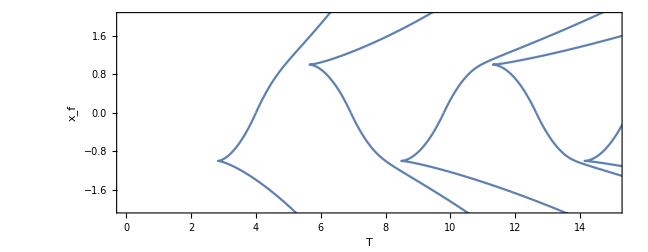

```mathematica
Clear[n,vi,xi,g];
xi=1;g=1;
gr2=Show[{
(*-------- Plot one branch --------*)
Table[
ParametricPlot[{
(2n)/g*(2 vi^2+2g xi+2n vi √(vi^2+2g xi))/(√(vi^2+2g xi)+2n vi),
(xi+vi^2/(2g)-g/2((2n)/g*(2 vi^2+2g xi+2n vi √(vi^2+2g xi))/(√(vi^2+2g xi)+2n vi)-vi/g-(2 √(vi^2+2g xi))/g n)^2)(-1)^n
},{vi,-1/(√2 √(n^2+n)),2}]
,{n,1,6}],
(*-------- Plot the other branch --------*)
Table[
ParametricPlot[{
(2n)/g*(2 vi^2+2g xi+2n vi √(vi^2+2g xi))/(√(vi^2+2g xi)+2n vi),
(xi+vi^2/(2g)-g/2((2n)/g*(2 vi^2+2g xi+2n vi √(vi^2+2g xi))/(√(vi^2+2g xi)+2n vi)-vi/g-(2 √(vi^2+2g xi))/g n)^2)(-1)^n
},{vi,-2,-1/(√2 √(n^2-n))}]
,{n,2,6}]
},
PlotRange->{{0,15},{-2,2}},PlotRangePadding->0,
ImageSize->{648,126*2},AspectRatio->Full,Axes->False,
FrameLabel->{"T","x_f"}]
```

#### Comparison of phase diagrams of one-sided bouncer and symmetric bouncer

```mathematica
Clear[n,vi,xi,g];
xi=1;g=1;
gr1=Show[
Table[
ParametricPlot[{
(2n)/g*(2 vi^2+2g xi+2n vi √(vi^2+2g xi))/(√(vi^2+2g xi)+2n vi),
xi+vi^2/(2g)-g/2((2n)/g*(2 vi^2+2g xi+2n vi √(vi^2+2g xi))/(√(vi^2+2g xi)+2n vi)-vi/g-(2 √(vi^2+2g xi))/g n)^2
},{vi,-1/(√2 √(n^2+n)),2},PlotStyle->{{Dashed,CapForm@"Butt",AbsoluteThickness@3,ColorData[97][2]}}]
,{n,1,6}],
ImageSize->{648,162},AspectRatio->Full,PlotRange->{{0,15},{0,2}},FrameLabel->{"T","x_f"}];
```

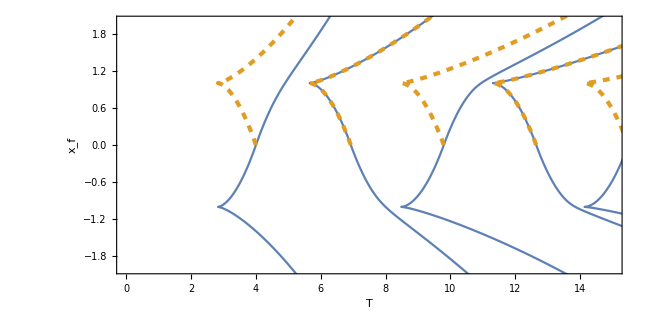

```mathematica
Show[gr2,gr1,PlotRange->{{0,15},{-2,2}},ImageSize->{648,162*2},Axes->True,AxesOrigin->{0,0},AxesStyle->LightGray]
```

In the figure above, the dashed orange curves are the caustics (phase boundaries) of the one-sided bouncer.  The solid blue curves are the caustics of the two-sided bouncer.  We see that these boundaries are related to each other by reflection.